# Notebook for : Soliton Solutions In Spacetime With Two Spacelike Killing Fields by Verdaguer

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 16, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article and Related Books

```mathematica
Hyperlink["Soliton Solutions In Spacetime With Two Spacelike Killing Fields by Verdaguer",
"https://www.sciencedirect.com/science/article/abs/pii/0370157393901395?via%3Dihub"]
```

[Soliton Solutions In Spacetime With Two Spacelike Killing Fields by Verdaguer](https://www.sciencedirect.com/science/article/abs/pii/0370157393901395?via%3Dihub)

```mathematica
(* Page 188 - introduced terms googol suggested by young Nephew *) 
Hyperlink["Kasner Biography",
"http://www.nasonline.org/publications/biographical-memoirs/memoir-pdfs/kasner-edward.pdf"]
```

[Kasner Biography](http://www.nasonline.org/publications/biographical-memoirs/memoir-pdfs/kasner-edward.pdf)

```mathematica
Hyperlink["Colliding Plane Waves by Griffiths - Book","ftp://nozdr.ru/biblio/kolxoz/P/PGr/Griffiths%20J.B.%20Colliding%20plane%20waves%20in%20general%20relativity%20(OUP,%201991)(ISBN%200198532091)(254s)_PGr_.pdf"]
```

[Colliding Plane Waves by Griffiths - Book](ftp://nozdr.ru/biblio/kolxoz/P/PGr/Griffiths%20J.B.%20Colliding%20plane%20waves%20in%20general%20relativity%20(OUP,%201991)(ISBN%200198532091)(254s)_PGr_.pdf)

```mathematica
Hyperlink["Exact Solutions To Einstein's Field Equations by Stephani et al",
"http://strangebeautiful.com/other-texts/stephani-et-exact-solns-efe.pdf"]
```

[Exact Solutions To Einstein's Field Equations by Stephani et al](http://strangebeautiful.com/other-texts/stephani-et-exact-solns-efe.pdf)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 286 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,VariationalMethods`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[Subscript[Z, 0]] -> Subscript[dZ, 0] ,
Dt[Subscript[Z, 1]] -> Subscript[dZ, 1] ,
Dt[Subscript[Z, 2]]-> Subscript[dZ, 2] ,
Dt[Subscript[Z, 3]]-> Subscript[dZ, 3] ,
Dt[Subscript[Z, 4]] -> Subscript[dZ, 4] ,
 Dt[Subscript[η, 0]]-> Subscript[dη, 0] , 
 Dt[Subscript[t, 0]]-> Subscript[dt, 0] , 
 Dt[t]-> dt ,
 Dt[T]-> dT ,
Dt[X]-> dX , 
Dt[Z]-> dZ , 
Dt[ξ]-> dξ , 
Dt[ψ]-> dψ , 
Dt[χ] -> dχ , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[φ]-> dφ , 
Dt[η] -> dη  ,
Dt[R] -> dR  ,
Dt[b]-> db , 
Dt[r]-> dr , 
Dt[u]-> du , 
Dt[v]-> dv , 
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[𝓊]-> d𝓊 , 
Dt[𝓍]-> d𝓍 , 
Dt[Subscript[t, -1]]-> Subscript[dt, -1] , 
Dt[Subscript[t, b]]-> Subscript[dt, b] ,
Dt[Subscript[z, b]]-> Subscript[dz, b] ,
Dt[Subscript[t, k]] -> Subscript[dt, k] ,
Dt[Subscript[z, k]] -> Subscript[dz, k] ,
Dt[τ]-> dτ ,  
Dt[ρ] -> dρ 
} ;
dtReplace // TableForm
```

Dt[Z] Subscript^(1,0)[Z,0]→dZ_0
Dt[Z] Subscript^(1,0)[Z,1]→dZ_1
Dt[Z] Subscript^(1,0)[Z,2]→dZ_2
Dt[Z] Subscript^(1,0)[Z,3]→dZ_3
Dt[Z] Subscript^(1,0)[Z,4]→dZ_4
Dt[η] Subscript^(1,0)[η,0]→dη_0
Dt[t] Subscript^(1,0)[t,0]→dt_0
Dt[t]→dt
Dt[T]→dT
Dt[X]→dX
Dt[Z]→dZ
Dt[ξ]→dξ
Dt[ψ]→dψ
Dt[χ]→dχ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[φ]→dφ
Dt[η]→dη
Dt[R]→dR
Dt[b]→db
Dt[r]→dr
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[t] Subscript^(1,0)[t,-1]→dt_-1
Dt[b] Subscript^(0,1)[t,b]+Dt[t] Subscript^(1,0)[t,b]→dt_b
Dt[b] Subscript^(0,1)[z,b]+Dt[z] Subscript^(1,0)[z,b]→dz_b
Dt[k] Subscript^(0,1)[t,k]+Dt[t] Subscript^(1,0)[t,k]→dt_k
Dt[k] Subscript^(0,1)[z,k]+Dt[z] Subscript^(1,0)[z,k]→dz_k
Dt[τ]→dτ
Dt[ρ]→dρ

```mathematica
(* b/:Dt[b]=0  ;  *)  (* for transform 37 *)
```

```mathematica
rs/:Dt[rs]=0   ;(* Schwarzschild radius equation 2.2.35 *) 
rg/:Dt[rg]=0   ;  
α/:Dt[α]=0   ; (* De Sitter equation 2.21.9 *) 
ω/:Dt[ω]=0   ;  (* 2.2.28 *) 
d/:Dt[d]=0   ;   (*  transformation 3.4 *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Section 2: Recasting of Einstein’s Equations and the Inverse Scattering Method Algorithm

```mathematica
Clear[eq2pt6]
eq2pt6[U_,V_,α_,β_]:= 
DeleteCases[Thread[Flatten[D[U,α] - D[V,β]] == Flatten[ConstantArray[0,{2,2}]]],True, Infinity]
```

```mathematica
Clear[eq2pt7a]
eq2pt7a[f_,U_,V_,α_,β_]:= 
D[Log[f],α] == (-1/α) + (1/(4α)) Tr[U.U + V . V ]
```

```mathematica
Clear[eq2pt7b]
eq2pt7b[f_,U_,V_,α_,β_]:= 
D[Log[f],β] == (1/(2α)) Tr[U . V ]
```

```mathematica
Clear[eq2pt8a]
eq2pt8a[g_,α_,β_] :=
U[α,β] ==(  α D[g,α] . Inverse[g] // Expand // FullSimplify )  ;
```

```mathematica
Clear[eq2pt8b]
eq2pt8b[g_,α_,β_] := 
V[α,β] ==(  α D[g,β] . Inverse[g] // Expand // FullSimplify )  ;
```

```mathematica
Clear[eq2pt9a]
eq2pt9a[ψ_,U_,V_,α_,β_] := 
Thread[Flatten[D[ψ,β] - ((2 λ^2)/(λ^2-α^2)) D[ψ,λ] ]==  Flatten[(-1)((α V + λ U)/(λ^2-α^2)) . ψ ] ]
```

```mathematica
Clear[eq2pt9b]
eq2pt9b[ψ_,U_,V_,α_,β_] := 
Thread[Flatten[D[ψ,β] + ((2 λ α)/(λ^2-α^2)) D[ψ,λ]] ==  Flatten[(-1)((α U + λ V)/(λ^2-α^2)) . ψ ]]
```

```mathematica
(*
Step one: "One starts by choosing the number n and by specifying whether the pole trajectories are real or complex"
*)
```

```mathematica
Clear[eq2pt11a] (* epsilon should be set to either plus or minus one *) 
eq2pt11a[i_,ϵ_,α_,β_]:= 
μ[i][α,β] == u[i][α,β] - β + ϵ √((u[i][α,β]-β)^2-α^2)
```

```mathematica
Clear[eq2pt11b] 
eq2pt11b[i_,α_,β_]:=  { 
D[μ[i][α,β],β] == ((2 (μ[i][α,β])^2)/(α^2- (μ[i][α,β])^2)) , 
D[μ[i][α,β],α] == ((2 α μ[i][α,β])/(α^2- (μ[i][α,β])^2))
} ;
```

```mathematica
(*
From the Subscript[ψ, 0] matrix associated with a given seed metric Subscript[g, 0] one constructs the vectors (next line) where the mo are arbitrary real or complex parameters. 
*)
```

```mathematica
(* Figure out how to do this.... *) 
Clear[eq2pt12a]
eq2pt12a[i_,α_,β_]:= 
 m[i]
```

```mathematica
(*
The next step is the construction of the n x n matrices Γ and the inverses D = Γ^-1
*)
```

```mathematica
(* Figure out how to do this.... *) 
Clear[eq2pt12b]
eq2pt12b[i_,α_,β_]:= 
m[i]
```

```mathematica
(* Figure out how to do this... *) 
Clear[eq2pt13]
eq2pt13[i_,α_,β_] := 
gprime[i]
```

```mathematica
Clear[eq2pt14a]
eq2pt14a[i_,α_,β_] := 
gprime[i]
```

```mathematica
(*
Step 3:  Afterthesolution for g has been found,we can calculate the metric coefficient f integrating eqs.(2.7)
*)
```

```mathematica
(*  Figure out how to do this *) 
Clear[eq2pt14b]
eq2pt14b[i_,α_,β_]:= 
α[i]
```

```mathematica
(*
"To summarize, give a seed metroc (f0,g0) ones uses g0 in (2.9) and solve for the generating matrix ψ0, then via (2.12) and (2.13) one can write down the final solution 2.14 "
*)
```

## Line Element and Metric 3.3 3.6

```mathematica
Clear[eq3pt3]
eq3pt3 = 
t^((d^2-1)/2)( dz^2- dt^2) + t^(1+d) dx^2+ t^(1-d) dy^2
```

dy^2 t^(1-d)+dx^2 t^(1+d)+(-dt^2+dz^2) t^(1/2 (-1+d^2))

```mathematica
lineToMetric[ eq3pt3 , {dt,dz,dx,dy}] // MatrixForm
```

(-t^(1/2 (-1+d^2)) | 0 | 0 | 0
0 | t^(1/2 (-1+d^2)) | 0 | 0
0 | 0 | t^(1+d) | 0
0 | 0 | 0 | t^(1-d))

```mathematica
Clear[eq3pt5]
eq3pt5 = { 
p1 == 2 ((1+d)/(d^2+3)) , 
p2 == 2 ((1-d)/(d^2+3)) , 
p3 == ((d^2-1)/(d^2+3))
} ;
eq3pt5   /. Equal-> Rule // TableForm
```

p1→(2 (1+d))/(3+d^2)
p2→(2 (1-d))/(3+d^2)
p3→(-1+d^2)/(3+d^2)

```mathematica
Clear[eq3pt4]
eq3pt4 = 
- dT^2+ T^(2 p1) dx^2 + T^(2p2) dy^2 +T^(2 p3) dz^2
```

-dT^2+dx^2 T^(2 p1)+dy^2 T^(2 p2)+dz^2 T^(2 p3)

```mathematica
Clear[eq3pt4a]
eq3pt4a = { 
p1^2+p2^2+p3^2 == 1,
p1+p2+p3==1 
} ;
eq3pt4a // TableForm
```

p1^2+p2^2+p3^2==1
p1+p2+p3==1

```mathematica
eq3pt4a[[1]]  
eq3pt4a[[1]]   /. (eq3pt5   /. Equal-> Rule ) 
eq3pt4a[[1]]   /. (eq3pt5   /. Equal-> Rule )  // Expand // Simplify
```

p1^2+p2^2+p3^2==1

(4 (1-d)^2)/((3+d^2)^2)+(4 (1+d)^2)/((3+d^2)^2)+((-1+d^2)^2)/((3+d^2)^2)==1

True

```mathematica
eq3pt4a[[2]]  
eq3pt4a[[2]]   /. (eq3pt5   /. Equal-> Rule ) 
eq3pt4a[[2]]   /. (eq3pt5   /. Equal-> Rule )  // Expand // Simplify
```

p1+p2+p3==1

(2 (1-d))/(3+d^2)+(2 (1+d))/(3+d^2)+(-1+d^2)/(3+d^2)==1

True

```mathematica
Clear[eq3pt4b]
eq3pt4b = 
T ==  t^((d^2+3)/4)
```

T==t^(1/4 (3+d^2))

```mathematica
eq3pt4b /. Equal-> Rule
```

T→t^(1/4 (3+d^2))

```mathematica
Dt[ eq3pt4b  ]  /. dtReplace  /. Equal-> Rule
```

dT→1/4 (3+d^2) dt t^(-1+1/4 (3+d^2))

```mathematica
eq3pt4
```

-dT^2+dx^2 T^(2 p1)+dy^2 T^(2 p2)+dz^2 T^(2 p3)

```mathematica
eq3pt4 /.(  eq3pt5   /. Equal-> Rule  )
```

-dT^2+dy^2 T^((4 (1-d))/(3+d^2))+dx^2 T^((4 (1+d))/(3+d^2))+dz^2 T^((2 (-1+d^2))/(3+d^2))

```mathematica
Clear[intermediate3pt3]
intermediate3pt3 = 
( eq3pt4 /.(  eq3pt5   /. Equal-> Rule  )) /. ( eq3pt4b /. Equal-> Rule  )  /. (Dt[ eq3pt4b  ]  /. dtReplace  /. Equal-> Rule )  // Expand // Simplify  ;
```

```mathematica
lineToMetric[ intermediate3pt3 , {dt,dz,dx,dy}] // Expand //PowerExpand // FullSimplify  // MatrixForm 

(* how could that be so close and just off in the t component? *)
```

(-1/16 (3+d^2)^2 t^(1/2 (-1+d^2)) | 0 | 0 | 0
0 | t^(1/2 (-1+d^2)) | 0 | 0
0 | 0 | t^(1+d) | 0
0 | 0 | 0 | t^(1-d))

```mathematica
Clear[eq3pt6]
eq3pt6 = 
f[t,z] ( dz^2- dt^2) + g11[t,z] dx^2+ g22[t,z] dy^2
```

(-dt^2+dz^2) f[t,z]+dx^2 g11[t,z]+dy^2 g22[t,z]

```mathematica
Clear[metric3pt6]
metric3pt6 = 
lineToMetric[ eq3pt6 , {dt,dz,dx,dy}] ;
metric3pt6  // MatrixForm
```

(-f[t,z] | 0 | 0 | 0
0 | f[t,z] | 0 | 0
0 | 0 | g11[t,z] | 0
0 | 0 | 0 | g22[t,z])

```mathematica
Clear[inverse3pt6]
inverse3pt6 = 
Inverse[metric3pt6 ] ;
inverse3pt6 // MatrixForm
```

(-1/f[t,z] | 0 | 0 | 0
0 | 1/f[t,z] | 0 | 0
0 | 0 | 1/g11[t,z] | 0
0 | 0 | 0 | 1/g22[t,z])

```mathematica
metric3pt6  . inverse3pt6  // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
inverse3pt6  . metric3pt6   // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Tensors Calculated For Metric 3.6 (The Riemann Tensor Needs To Be Converted to a 6x6 Matrix For Formulas To Match - REDO THIS!!)

```mathematica
Clear[input3pt6] 
input3pt6[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList3pt6];
tensorList3pt6 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList3pt6[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList3pt6[[2]]  = 
ChristoffelSymbol[ tensorList3pt6[[1]] , ActWith-> Simplify] ;
tensorList3pt6[[3]] = 
RiemannTensor[ tensorList3pt6[[1]] , ActWithNested-> Simplify ];
tensorList3pt6[[4]] = 
RicciTensor[ tensorList3pt6[[1]] , ActWith-> Simplify ] ;
tensorList3pt6[[5]] = 
RicciScalar[ tensorList3pt6[[1]] , ActWith-> Simplify ] ;
tensorList3pt6[[6]] = 
KretschmannScalar[ tensorList3pt6[[1]] , ActWith-> Simplify] ; 
tensorList3pt6[[7]] = 
EinsteinTensor[ tensorList3pt6[[1]] , ActWith-> Simplify] ; 
tensorList3pt6[[8]] = 
WeylTensor[ tensorList3pt6[[1]] , ActWith-> Simplify ] ; 
 tensorList3pt6[[9]] = 
CottonTensor[ tensorList3pt6[[1]] , ActWith-> Simplify ]  ;
];
```

```mathematica
(* Note ordereding for B12 and t,z *) 
(* Last timing took 10.48 for all tensors except *) 
input3pt6[ "metric3pt6", metric3pt6, "3pt6","g^diagonal",{t,z,x,y}, "Greek"] // Timing
```

{9.84901,Null}

```mathematica
tensorList3pt6
```

{(g^diagonal)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList3pt6[[1]]
TensorName[tensorList3pt6[[1]]]
TensorValues[tensorList3pt6[[1]]] // MatrixForm // pdConv
```

(g^diagonal)_αβ^

3pt6

(-f(t,z) | 0 | 0 | 0
0 | f(t,z) | 0 | 0
0 | 0 | g11(t,z) | 0
0 | 0 | 0 | g22(t,z))

```mathematica
tensorList3pt6[[2]]
TensorName[tensorList3pt6[[2]]]
TensorValues[tensorList3pt6[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbol3pt6

((((∂f(t,z))/(∂t))/(2 f(t,z))
((∂f(t,z))/(∂z))/(2 f(t,z))
0
0) | (((∂f(t,z))/(∂z))/(2 f(t,z))
((∂f(t,z))/(∂t))/(2 f(t,z))
0
0) | (0
0
((∂g11(t,z))/(∂t))/(2 f(t,z))
0) | (0
0
0
((∂g22(t,z))/(∂t))/(2 f(t,z)))
(((∂f(t,z))/(∂z))/(2 f(t,z))
((∂f(t,z))/(∂t))/(2 f(t,z))
0
0) | (((∂f(t,z))/(∂t))/(2 f(t,z))
((∂f(t,z))/(∂z))/(2 f(t,z))
0
0) | (0
0
-((∂g11(t,z))/(∂z))/(2 f(t,z))
0) | (0
0
0
-((∂g22(t,z))/(∂z))/(2 f(t,z)))
(0
0
((∂g11(t,z))/(∂t))/(2 g11(t,z))
0) | (0
0
((∂g11(t,z))/(∂z))/(2 g11(t,z))
0) | (((∂g11(t,z))/(∂t))/(2 g11(t,z))
((∂g11(t,z))/(∂z))/(2 g11(t,z))
0
0) | (0
0
0
0)
(0
0
0
((∂g22(t,z))/(∂t))/(2 g22(t,z))) | (0
0
0
((∂g22(t,z))/(∂z))/(2 g22(t,z))) | (0
0
0
0) | (((∂g22(t,z))/(∂t))/(2 g22(t,z))
((∂g22(t,z))/(∂z))/(2 g22(t,z))
0
0))

```mathematica
tensorList3pt6[[3]]
TensorName[tensorList3pt6[[3]]]
TensorValues[tensorList3pt6[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensor3pt6

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2)/(2 f(t,z)) | 0 | 0
-(f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2)/(2 f(t,z)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/4 (((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))-2 (∂^2 g11(t,z))/(∂t^2)+((∂g11(t,z))/(∂t))^2/(g11(t,z))) | 0
0 | 0 | 1/4 (-2 (∂^2 g11(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
1/4 (-((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+2 (∂^2 g11(t,z))/(∂t^2)-((∂g11(t,z))/(∂t))^2/(g11(t,z))) | 1/4 (2 (∂^2 g11(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/4 (((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))-2 (∂^2 g22(t,z))/(∂t^2)+((∂g22(t,z))/(∂t))^2/(g22(t,z)))
0 | 0 | 0 | 1/4 (-2 (∂^2 g22(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z)))
0 | 0 | 0 | 0
1/4 (-((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+2 (∂^2 g22(t,z))/(∂t^2)-((∂g22(t,z))/(∂t))^2/(g22(t,z))) | 1/4 (2 (∂^2 g22(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))-((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))) | 0 | 0)
(0 | -(f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2)/(2 f(t,z)) | 0 | 0
(f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2)/(2 f(t,z)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/4 (-2 (∂^2 g11(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
0 | 0 | 1/4 (((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))-2 (∂^2 g11(t,z))/(∂z^2)+((∂g11(t,z))/(∂z))^2/(g11(t,z))) | 0
1/4 (2 (∂^2 g11(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 1/4 (-((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+2 (∂^2 g11(t,z))/(∂z^2)-((∂g11(t,z))/(∂z))^2/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/4 (-2 (∂^2 g22(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z)))
0 | 0 | 0 | 1/4 (((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))-2 (∂^2 g22(t,z))/(∂z^2)+((∂g22(t,z))/(∂z))^2/(g22(t,z)))
0 | 0 | 0 | 0
1/4 (2 (∂^2 g22(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))-((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))) | 1/4 (-((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+2 (∂^2 g22(t,z))/(∂z^2)-((∂g22(t,z))/(∂z))^2/(g22(t,z))) | 0 | 0)
(0 | 0 | 1/4 (-((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+2 (∂^2 g11(t,z))/(∂t^2)-((∂g11(t,z))/(∂t))^2/(g11(t,z))) | 0
0 | 0 | 1/4 (2 (∂^2 g11(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
1/4 (((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))-2 (∂^2 g11(t,z))/(∂t^2)+((∂g11(t,z))/(∂t))^2/(g11(t,z))) | 1/4 (-2 (∂^2 g11(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/4 (2 (∂^2 g11(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
0 | 0 | 1/4 (-((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+2 (∂^2 g11(t,z))/(∂z^2)-((∂g11(t,z))/(∂z))^2/(g11(t,z))) | 0
1/4 (-2 (∂^2 g11(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 1/4 (((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))-2 (∂^2 g11(t,z))/(∂z^2)+((∂g11(t,z))/(∂z))^2/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(4 f(t,z))
0 | 0 | -((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(4 f(t,z)) | 0)
(0 | 0 | 0 | 1/4 (-((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+2 (∂^2 g22(t,z))/(∂t^2)-((∂g22(t,z))/(∂t))^2/(g22(t,z)))
0 | 0 | 0 | 1/4 (2 (∂^2 g22(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))-((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z)))
0 | 0 | 0 | 0
1/4 (((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))-2 (∂^2 g22(t,z))/(∂t^2)+((∂g22(t,z))/(∂t))^2/(g22(t,z))) | 1/4 (-2 (∂^2 g22(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))) | 0 | 0) | (0 | 0 | 0 | 1/4 (2 (∂^2 g22(t,z))/(∂t ∂z)-((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))-((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z)))
0 | 0 | 0 | 1/4 (-((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+2 (∂^2 g22(t,z))/(∂z^2)-((∂g22(t,z))/(∂z))^2/(g22(t,z)))
0 | 0 | 0 | 0
1/4 (-2 (∂^2 g22(t,z))/(∂t ∂z)+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z))+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))) | 1/4 (((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))-2 (∂^2 g22(t,z))/(∂z^2)+((∂g22(t,z))/(∂z))^2/(g22(t,z))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(4 f(t,z))
0 | 0 | ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(4 f(t,z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList3pt6[[4]]
TensorName[tensorList3pt6[[4]]]
TensorValues[tensorList3pt6[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensor3pt6

(1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+(2 (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂t))^2/(g11(t,z))^2+((∂g22(t,z))/(∂t))^2/(g22(t,z))^2) | 1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))^2+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))^2) | 0 | 0
1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))^2+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))^2) | 1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+(2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂z))^2/(g11(t,z))^2+((∂g22(t,z))/(∂z))^2/(g22(t,z))^2) | 0 | 0
0 | 0 | (g22(t,z) (-2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)+g11(t,z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(4 f(t,z) g11(t,z) g22(t,z)) | 0
0 | 0 | 0 | (g22(t,z) (-2 g11(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+g11(t,z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2))/(4 f(t,z) g11(t,z) g22(t,z)))

```mathematica
tensorList3pt6[[5]]
TensorName[tensorList3pt6[[5]]]
TensorValues[tensorList3pt6[[5]]] // MatrixForm // pdConv
```

R

RicciScalar3pt6

1/(2 (f(t,z))^3 (g11(t,z))^2 (g22(t,z))^2)((f(t,z))^2 g11(t,z) g22(t,z) (-2 g22(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z))^2 (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))+2 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2))+(f(t,z))^2 (g22(t,z))^2 (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2))

```mathematica
tensorList3pt6[[6]]
TensorName[tensorList3pt6[[6]]]
TensorValues[tensorList3pt6[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalar3pt6

1/(4 (f(t,z))^6 (g11(t,z))^4 (g22(t,z))^4)(((((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)^2 (f(t,z))^4-2 ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)+(∂f(t,z))/(∂z) (((∂g22(t,z))/(∂t))^2 (∂g22(t,z))/(∂z)-((∂g22(t,z))/(∂z))^3)+2 ((∂^2 g22(t,z))/(∂t^2) ((∂g22(t,z))/(∂t))^2-2 (∂g22(t,z))/(∂z) (∂^2 g22(t,z))/(∂t ∂z) (∂g22(t,z))/(∂t)+((∂g22(t,z))/(∂z))^2 (∂^2 g22(t,z))/(∂z^2)) f(t,z)) g22(t,z) (f(t,z))^3+2 ((((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2) ((∂f(t,z))/(∂t))^2-2 ((∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)+(∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)-2 (∂g22(t,z))/(∂z) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z) (∂f(t,z))/(∂t)+2 (((∂^2 g22(t,z))/(∂t^2))^2+((∂^2 g22(t,z))/(∂z^2))^2-2 ((∂^2 g22(t,z))/(∂t ∂z))^2) (f(t,z))^2+((∂f(t,z))/(∂z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)-2 (∂f(t,z))/(∂z) ((∂g22(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))-2 (∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) (g22(t,z))^2 (f(t,z))^2+4 (-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2+((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2)) f(t,z))^2 (g22(t,z))^4) (g11(t,z))^4+(((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))^2 (g22(t,z))^2 (f(t,z))^4+2 ((((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) ((∂f(t,z))/(∂t))^2-2 ((∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)+(∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)-2 (∂g11(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z) (∂f(t,z))/(∂t)+2 (((∂^2 g11(t,z))/(∂t^2))^2+((∂^2 g11(t,z))/(∂z^2))^2-2 ((∂^2 g11(t,z))/(∂t ∂z))^2) (f(t,z))^2+((∂f(t,z))/(∂z))^2 (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)-2 (∂f(t,z))/(∂z) ((∂g11(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))-2 (∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)) (g22(t,z))^4 (f(t,z))^2) (g11(t,z))^2-2 (f(t,z))^3 ((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)+(∂f(t,z))/(∂z) (((∂g11(t,z))/(∂t))^2 (∂g11(t,z))/(∂z)-((∂g11(t,z))/(∂z))^3)+2 ((∂^2 g11(t,z))/(∂t^2) ((∂g11(t,z))/(∂t))^2-2 (∂g11(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z) (∂g11(t,z))/(∂t)+((∂g11(t,z))/(∂z))^2 (∂^2 g11(t,z))/(∂z^2)) f(t,z)) (g22(t,z))^4 g11(t,z)+(((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)^2 (f(t,z))^4 (g22(t,z))^4)

```mathematica
tensorList3pt6[[7]]
TensorName[tensorList3pt6[[7]]]
TensorValues[tensorList3pt6[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensor3pt6

(((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))+f(t,z) ((∂g22(t,z))/(∂z))^2)+g11(t,z) g22(t,z) (g22(t,z) (-2 f(t,z) (∂^2 g11(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))+f(t,z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)))+f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂z))^2)/(4 f(t,z) (g11(t,z))^2 (g22(t,z))^2) | 1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))^2+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))^2) | 0 | 0
1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))^2+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))^2) | ((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))+f(t,z) ((∂g22(t,z))/(∂t))^2)+g11(t,z) g22(t,z) (g22(t,z) (-2 f(t,z) (∂^2 g11(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))+f(t,z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)))+f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂t))^2)/(4 f(t,z) (g11(t,z))^2 (g22(t,z))^2) | 0 | 0
0 | 0 | (g11(t,z) (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))-2 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2)))/(4 (f(t,z))^3 (g22(t,z))^2) | 0
0 | 0 | 0 | (g22(t,z) (2 (f(t,z))^2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-2 (g11(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2)))/(4 (f(t,z))^3 (g11(t,z))^2))

```mathematica
tensorList3pt6[[8]]
TensorName[tensorList3pt6[[8]]]
TensorValues[tensorList3pt6[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensor3pt6

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (((f(t,z))^2 (-2 g11(t,z) g22(t,z) (g11(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g22(t,z))^2 (-2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)+(g11(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)))/((g11(t,z))^2 (g22(t,z))^2)+4 f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+4 ((∂f(t,z))/(∂t))^2-4 ((∂f(t,z))/(∂z))^2)/(24 f(t,z)) | 0 | 0
(((f(t,z))^2 (2 g11(t,z) g22(t,z) (g11(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g22(t,z))^2 (2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2)+(g11(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2)))/((g11(t,z))^2 (g22(t,z))^2)+4 f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-4 ((∂f(t,z))/(∂t))^2+4 ((∂f(t,z))/(∂z))^2)/(24 f(t,z)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/24 ((g11(t,z) (2 f(t,z) ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+(-2 f(t,z) (2 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+(2 g11(t,z) (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))-(g11(t,z) (((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+(2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 0
0 | 0 | 1/8 ((g11(t,z) (2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)-(∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(g22(t,z))^2-2 (∂^2 g11(t,z))/(∂t ∂z)+(g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))-g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
1/24 ((3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))-g22(t,z) (-2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))+(2 g11(t,z) (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+(-2 g11(t,z) ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))+(g11(t,z) (((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+4 (∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2)-(2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 1/8 ((g11(t,z) ((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)-2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)))/(g22(t,z))^2+2 (∂^2 g11(t,z))/(∂t ∂z)+(g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))-g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/24 ((g22(t,z) (2 f(t,z) ((∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g11(t,z))+(-2 f(t,z) (2 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+(2 g22(t,z) (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g11(t,z))-(g22(t,z) (((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+(2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2)/(g22(t,z)))
0 | 0 | 0 | -(-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z))
0 | 0 | 0 | 0
1/24 ((g22(t,z) (2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))-3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g11(t,z))+(2 g22(t,z) (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+(g22(t,z) (-2 g11(t,z) ((∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2))+((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g11(t,z))+4 (∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2)-(2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2)/(g22(t,z))) | (-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z)) | 0 | 0)
(0 | (((f(t,z))^2 (2 g11(t,z) g22(t,z) (g11(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g22(t,z))^2 (2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2)+(g11(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2)))/((g11(t,z))^2 (g22(t,z))^2)+4 f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-4 ((∂f(t,z))/(∂t))^2+4 ((∂f(t,z))/(∂z))^2)/(24 f(t,z)) | 0 | 0
(((f(t,z))^2 (-2 g11(t,z) g22(t,z) (g11(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g22(t,z))^2 (-2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)+(g11(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)))/((g11(t,z))^2 (g22(t,z))^2)+4 f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+4 ((∂f(t,z))/(∂t))^2-4 ((∂f(t,z))/(∂z))^2)/(24 f(t,z)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/8 ((g11(t,z) (2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)-(∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(g22(t,z))^2-2 (∂^2 g11(t,z))/(∂t ∂z)+(g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))-g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
0 | 0 | 1/24 ((g11(t,z) (2 f(t,z) (2 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+(-2 f(t,z) ((∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+(2 g11(t,z) (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g22(t,z))-(g11(t,z) (2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+(((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 0
1/8 ((g11(t,z) ((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)-2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)))/(g22(t,z))^2+2 (∂^2 g11(t,z))/(∂t ∂z)+(g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))-g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 1/24 ((3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))-g22(t,z) (2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))+(2 g11(t,z) (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2))/(f(t,z))^2+(-2 g11(t,z) (2 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))+(g11(t,z) (2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+2 (∂^2 g11(t,z))/(∂t^2)+4 (∂^2 g11(t,z))/(∂z^2)-(((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z))
0 | 0 | 0 | 1/24 ((g22(t,z) (2 f(t,z) (2 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g11(t,z))+(-2 f(t,z) ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+(2 g22(t,z) (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g11(t,z))-(g22(t,z) (2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+(((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2)/(g22(t,z)))
0 | 0 | 0 | 0
(-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z)) | 1/24 ((g22(t,z) (-2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))-3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g11(t,z))+(2 g22(t,z) (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2))/(f(t,z))^2+(g22(t,z) (-2 g11(t,z) (2 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))+2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g11(t,z))+2 ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))-(((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2)/(g22(t,z))) | 0 | 0)
(0 | 0 | 1/24 ((3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))-g22(t,z) (-2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))+(2 g11(t,z) (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+(-2 g11(t,z) ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))+(g11(t,z) (((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+4 (∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2)-(2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 0
0 | 0 | 1/8 ((g11(t,z) ((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)-2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)))/(g22(t,z))^2+2 (∂^2 g11(t,z))/(∂t ∂z)+(g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))-g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
1/24 ((g11(t,z) (2 f(t,z) ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+(-2 f(t,z) (2 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+(2 g11(t,z) (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))-(g11(t,z) (((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+(2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 1/8 ((g11(t,z) (2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)-(∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(g22(t,z))^2-2 (∂^2 g11(t,z))/(∂t ∂z)+(g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))-g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/8 ((g11(t,z) ((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)-2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)))/(g22(t,z))^2+2 (∂^2 g11(t,z))/(∂t ∂z)+(g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))-g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))-((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 0
0 | 0 | 1/24 ((3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))-g22(t,z) (2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g22(t,z))+(2 g11(t,z) (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2))/(f(t,z))^2+(-2 g11(t,z) (2 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))+(g11(t,z) (2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+2 (∂^2 g11(t,z))/(∂t^2)+4 (∂^2 g11(t,z))/(∂z^2)-(((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 0
1/8 ((g11(t,z) (2 g22(t,z) (∂^2 g22(t,z))/(∂t ∂z)-(∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(g22(t,z))^2-2 (∂^2 g11(t,z))/(∂t ∂z)+(g22(t,z) ((∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))-g11(t,z) ((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))) | 1/24 ((g11(t,z) (2 f(t,z) (2 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g22(t,z))+(-2 f(t,z) ((∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z))+(2 g11(t,z) (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g22(t,z))-(g11(t,z) (2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2))/(g22(t,z))^2+(((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2)/(g11(t,z))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 (f(t,z))^2 (g22(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z) (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+4 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2)))/(g22(t,z))+((f(t,z))^2 g22(t,z) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2))/(g11(t,z)))/(24 (f(t,z))^3)
0 | 0 | (-2 (f(t,z))^2 (g22(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z) (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))-4 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)))/(g22(t,z))+((f(t,z))^2 g22(t,z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2))/(g11(t,z)))/(24 (f(t,z))^3) | 0)
(0 | 0 | 0 | 1/24 ((g22(t,z) (2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))-3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g11(t,z))+(2 g22(t,z) (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+(g22(t,z) (-2 g11(t,z) ((∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2))+((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g11(t,z))+4 (∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2)-(2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2)/(g22(t,z)))
0 | 0 | 0 | (-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z))
0 | 0 | 0 | 0
1/24 ((g22(t,z) (2 f(t,z) ((∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g11(t,z))+(-2 f(t,z) (2 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+(2 g22(t,z) (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g11(t,z))-(g22(t,z) (((∂g11(t,z))/(∂t))^2+2 ((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+(2 ((∂g22(t,z))/(∂t))^2+((∂g22(t,z))/(∂z))^2)/(g22(t,z))) | -(-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z)) | 0 | 0) | (0 | 0 | 0 | (-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z))
0 | 0 | 0 | 1/24 ((g22(t,z) (-2 g11(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))-3 g11(t,z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(f(t,z) g11(t,z))+(2 g22(t,z) (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2))/(f(t,z))^2+(g22(t,z) (-2 g11(t,z) (2 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))+2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g11(t,z))+2 ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))-(((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2)/(g22(t,z)))
0 | 0 | 0 | 0
-(-((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+f(t,z) (∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)))+g11(t,z) (g22(t,z))^2 (-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))+f(t,z) (g22(t,z))^2 (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(8 f(t,z) (g11(t,z))^2 g22(t,z)) | 1/24 ((g22(t,z) (2 f(t,z) (2 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))-3 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z)))/(f(t,z) g11(t,z))+(-2 f(t,z) ((∂^2 g22(t,z))/(∂t^2)+2 (∂^2 g22(t,z))/(∂z^2))+3 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z))+(2 g22(t,z) (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g11(t,z))-(g22(t,z) (2 ((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2))/(g11(t,z))^2+(((∂g22(t,z))/(∂t))^2+2 ((∂g22(t,z))/(∂z))^2)/(g22(t,z))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (-2 (f(t,z))^2 (g22(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z) (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))-4 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)))/(g22(t,z))+((f(t,z))^2 g22(t,z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2))/(g11(t,z)))/(24 (f(t,z))^3)
0 | 0 | (2 (f(t,z))^2 (g22(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z) (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+4 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2)))/(g22(t,z))+((f(t,z))^2 g22(t,z) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2))/(g11(t,z)))/(24 (f(t,z))^3) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList3pt6[[9]]
TensorName[tensorList3pt6[[9]]]
TensorValues[tensorList3pt6[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensor3pt6

((0
((4 (∂g22(t,z))/(∂z) (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2) (f(t,z))^3+(2 ((∂g22(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)+4 (∂^2 g22(t,z))/(∂z^2))-5 (∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)-5 (∂f(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)) g22(t,z) (f(t,z))^2+2 (3 (∂g22(t,z))/(∂z) ((∂f(t,z))/(∂t))^2-2 ((∂^3 g22(t,z))/(∂z^3)-(∂^3 g22(t,z))/(∂t^2 ∂z)) (f(t,z))^2-3 ((∂f(t,z))/(∂z))^2 (∂g22(t,z))/(∂z)+3 ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2)) (∂g22(t,z))/(∂z) f(t,z)+2 (∂f(t,z))/(∂z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2)) f(t,z)) (g22(t,z))^2 f(t,z)+8 (3 ((∂f(t,z))/(∂z))^3+((2 (∂^2 f(t,z))/(∂t^2)-4 (∂^2 f(t,z))/(∂z^2)) f(t,z)-3 ((∂f(t,z))/(∂t))^2) (∂f(t,z))/(∂z)+f(t,z) (2 (∂f(t,z))/(∂t) (∂^2 f(t,z))/(∂t ∂z)+((∂^3 f(t,z))/(∂z^3)-(∂^3 f(t,z))/(∂t^2 ∂z)) f(t,z))) (g22(t,z))^3) (g11(t,z))^3-2 f(t,z) g22(t,z) ((∂g22(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) (f(t,z))^2+((∂f(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+((∂^2 g11(t,z))/(∂z^2) (∂g22(t,z))/(∂z)+(∂g11(t,z))/(∂z) (∂^2 g22(t,z))/(∂z^2)-(∂g22(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)-(∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) f(t,z)+(-3 (∂g11(t,z))/(∂z) ((∂f(t,z))/(∂t))^2+2 ((∂^3 g11(t,z))/(∂z^3)-(∂^3 g11(t,z))/(∂t^2 ∂z)) (f(t,z))^2+3 ((∂f(t,z))/(∂z))^2 (∂g11(t,z))/(∂z)+3 ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2)) (∂g11(t,z))/(∂z) f(t,z)+2 (∂f(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)-(∂^2 g11(t,z))/(∂z^2)) f(t,z)) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 (2 (∂g11(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)+(2 ((∂g11(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)+4 (∂^2 g11(t,z))/(∂z^2))-5 (∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)-5 (∂f(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂z) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^3 (g11(t,z))^3 (g22(t,z))^3)
0
0) | ((-((4 (∂g22(t,z))/(∂z) (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2) (f(t,z))^3+(2 ((∂g22(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)+4 (∂^2 g22(t,z))/(∂z^2))-5 (∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)-5 (∂f(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)) g22(t,z) (f(t,z))^2+2 (3 (∂g22(t,z))/(∂z) ((∂f(t,z))/(∂t))^2-2 ((∂^3 g22(t,z))/(∂z^3)-(∂^3 g22(t,z))/(∂t^2 ∂z)) (f(t,z))^2-3 ((∂f(t,z))/(∂z))^2 (∂g22(t,z))/(∂z)+3 ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2)) (∂g22(t,z))/(∂z) f(t,z)+2 (∂f(t,z))/(∂z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2)) f(t,z)) (g22(t,z))^2 f(t,z)+8 (3 ((∂f(t,z))/(∂z))^3+((2 (∂^2 f(t,z))/(∂t^2)-4 (∂^2 f(t,z))/(∂z^2)) f(t,z)-3 ((∂f(t,z))/(∂t))^2) (∂f(t,z))/(∂z)+f(t,z) (2 (∂f(t,z))/(∂t) (∂^2 f(t,z))/(∂t ∂z)+((∂^3 f(t,z))/(∂z^3)-(∂^3 f(t,z))/(∂t^2 ∂z)) f(t,z))) (g22(t,z))^3) (g11(t,z))^3)+2 f(t,z) g22(t,z) ((∂g22(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) (f(t,z))^2+((∂f(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+((∂^2 g11(t,z))/(∂z^2) (∂g22(t,z))/(∂z)+(∂g11(t,z))/(∂z) (∂^2 g22(t,z))/(∂z^2)-(∂g22(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)-(∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) f(t,z)+(-3 (∂g11(t,z))/(∂z) ((∂f(t,z))/(∂t))^2+2 ((∂^3 g11(t,z))/(∂z^3)-(∂^3 g11(t,z))/(∂t^2 ∂z)) (f(t,z))^2+3 ((∂f(t,z))/(∂z))^2 (∂g11(t,z))/(∂z)+3 ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2)) (∂g11(t,z))/(∂z) f(t,z)+2 (∂f(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)-(∂^2 g11(t,z))/(∂z^2)) f(t,z)) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 (2 (∂g11(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)+(5 (∂f(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)-2 ((∂g11(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)+4 (∂^2 g11(t,z))/(∂z^2))-5 (∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^3 (g11(t,z))^3 (g22(t,z))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
((4 (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2) (f(t,z))^3+(-5 (∂f(t,z))/(∂t) ((∂g22(t,z))/(∂z))^2+10 (∂^2 g22(t,z))/(∂t ∂z) f(t,z) (∂g22(t,z))/(∂z)+(∂g22(t,z))/(∂t) (5 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-2 (4 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2)) f(t,z))) g22(t,z) (f(t,z))^2+2 (-2 ((∂^3 g22(t,z))/(∂t ∂z^2)-(∂^3 g22(t,z))/(∂t^3)) (f(t,z))^2+(-3 (∂^2 f(t,z))/(∂t^2) (∂g22(t,z))/(∂t)+3 (∂^2 f(t,z))/(∂z^2) (∂g22(t,z))/(∂t)-2 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)+2 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)) f(t,z)+3 (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2) (∂g22(t,z))/(∂t)) (g22(t,z))^2 f(t,z)+8 (-3 ((∂f(t,z))/(∂t))^3+3 ((∂f(t,z))/(∂z))^2 (∂f(t,z))/(∂t)-2 ((∂^2 f(t,z))/(∂z^2)-2 (∂^2 f(t,z))/(∂t^2)) f(t,z) (∂f(t,z))/(∂t)+((∂^3 f(t,z))/(∂t ∂z^2)-(∂^3 f(t,z))/(∂t^3)) (f(t,z))^2-2 (∂f(t,z))/(∂z) (∂^2 f(t,z))/(∂t ∂z) f(t,z)) (g22(t,z))^3) (g11(t,z))^3-2 f(t,z) g22(t,z) (((∂g11(t,z))/(∂t) (((∂g22(t,z))/(∂t))^2-(∂^2 g22(t,z))/(∂t^2) g22(t,z))+g22(t,z) (-(∂^2 g11(t,z))/(∂t^2) (∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z)+2 ((∂^3 g11(t,z))/(∂t ∂z^2)-(∂^3 g11(t,z))/(∂t^3)) g22(t,z))+(∂g11(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t ∂z) g22(t,z)-(∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))) (f(t,z))^2+g22(t,z) ((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)+(3 (∂^2 f(t,z))/(∂t^2) (∂g11(t,z))/(∂t)-3 (∂^2 f(t,z))/(∂z^2) (∂g11(t,z))/(∂t)+2 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)-2 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)) g22(t,z)) f(t,z)+3 (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2) (∂g11(t,z))/(∂t) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 (2 (∂g11(t,z))/(∂t) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)+(-5 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z))^2+10 (∂^2 g11(t,z))/(∂t ∂z) f(t,z) (∂g11(t,z))/(∂z)+(∂g11(t,z))/(∂t) (5 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)-2 (4 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2)) f(t,z))) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^3 (g11(t,z))^3 (g22(t,z))^3)
0
0) | (((4 (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+(5 (∂f(t,z))/(∂t) ((∂g22(t,z))/(∂z))^2-10 (∂^2 g22(t,z))/(∂t ∂z) f(t,z) (∂g22(t,z))/(∂z)+(∂g22(t,z))/(∂t) (2 (4 (∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2)) f(t,z)-5 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t))) g22(t,z) (f(t,z))^2+2 (2 ((∂^3 g22(t,z))/(∂t ∂z^2)-(∂^3 g22(t,z))/(∂t^3)) (f(t,z))^2+(3 (∂^2 f(t,z))/(∂t^2) (∂g22(t,z))/(∂t)-3 (∂^2 f(t,z))/(∂z^2) (∂g22(t,z))/(∂t)+2 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)-2 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)) f(t,z)+3 (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2) (∂g22(t,z))/(∂t)) (g22(t,z))^2 f(t,z)-8 (-3 ((∂f(t,z))/(∂t))^3+3 ((∂f(t,z))/(∂z))^2 (∂f(t,z))/(∂t)-2 ((∂^2 f(t,z))/(∂z^2)-2 (∂^2 f(t,z))/(∂t^2)) f(t,z) (∂f(t,z))/(∂t)+((∂^3 f(t,z))/(∂t ∂z^2)-(∂^3 f(t,z))/(∂t^3)) (f(t,z))^2-2 (∂f(t,z))/(∂z) (∂^2 f(t,z))/(∂t ∂z) f(t,z)) (g22(t,z))^3) (g11(t,z))^3+2 f(t,z) g22(t,z) (((∂g11(t,z))/(∂t) (((∂g22(t,z))/(∂t))^2-(∂^2 g22(t,z))/(∂t^2) g22(t,z))+g22(t,z) (-(∂^2 g11(t,z))/(∂t^2) (∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z)+2 ((∂^3 g11(t,z))/(∂t ∂z^2)-(∂^3 g11(t,z))/(∂t^3)) g22(t,z))+(∂g11(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t ∂z) g22(t,z)-(∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))) (f(t,z))^2+g22(t,z) ((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)+(3 (∂^2 f(t,z))/(∂t^2) (∂g11(t,z))/(∂t)-3 (∂^2 f(t,z))/(∂z^2) (∂g11(t,z))/(∂t)+2 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)-2 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)) g22(t,z)) f(t,z)+3 (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2) (∂g11(t,z))/(∂t) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 (2 (∂g11(t,z))/(∂t) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)+(5 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z))^2-10 (∂^2 g11(t,z))/(∂t ∂z) f(t,z) (∂g11(t,z))/(∂z)+(∂g11(t,z))/(∂t) (2 (4 (∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2)) f(t,z)-5 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t))) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^3 (g11(t,z))^3 (g22(t,z))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(-2 (2 (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+2 ((∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)-(∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)+((∂^3 g22(t,z))/(∂t ∂z^2)-(∂^3 g22(t,z))/(∂t^3)) f(t,z)) (g22(t,z))^2 (f(t,z))^2+((∂f(t,z))/(∂t) ((∂g22(t,z))/(∂z))^2-2 (∂^2 g22(t,z))/(∂t ∂z) f(t,z) (∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+2 ((∂^2 g22(t,z))/(∂z^2)-2 (∂^2 g22(t,z))/(∂t^2)) f(t,z))) g22(t,z) (f(t,z))^2+2 (-3 ((∂f(t,z))/(∂t))^3+3 ((∂f(t,z))/(∂z))^2 (∂f(t,z))/(∂t)-2 ((∂^2 f(t,z))/(∂z^2)-2 (∂^2 f(t,z))/(∂t^2)) f(t,z) (∂f(t,z))/(∂t)+((∂^3 f(t,z))/(∂t ∂z^2)-(∂^3 f(t,z))/(∂t^3)) (f(t,z))^2-2 (∂f(t,z))/(∂z) (∂^2 f(t,z))/(∂t ∂z) f(t,z)) (g22(t,z))^3) (g11(t,z))^3+f(t,z) g22(t,z) (((∂g11(t,z))/(∂t) (((∂g22(t,z))/(∂t))^2+2 (∂^2 g22(t,z))/(∂t^2) g22(t,z))+4 g22(t,z) (-(∂^2 g11(t,z))/(∂t^2) (∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z)+2 ((∂^3 g11(t,z))/(∂t ∂z^2)-(∂^3 g11(t,z))/(∂t^3)) g22(t,z))-(∂g11(t,z))/(∂z) ((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)+2 (∂^2 g22(t,z))/(∂t ∂z) g22(t,z))) (f(t,z))^2+g22(t,z) ((∂g11(t,z))/(∂z) (3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)-(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))+(∂g11(t,z))/(∂t) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))+(6 (∂^2 f(t,z))/(∂t^2) (∂g11(t,z))/(∂t)-6 (∂^2 f(t,z))/(∂z^2) (∂g11(t,z))/(∂t)+8 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)-8 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)) g22(t,z)) f(t,z)+6 (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2) (∂g11(t,z))/(∂t) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂t) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)+(7 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z))^2-14 (∂^2 g11(t,z))/(∂t ∂z) f(t,z) (∂g11(t,z))/(∂z)+(∂g11(t,z))/(∂t) (-7 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)-2 ((∂^2 g11(t,z))/(∂z^2)-8 (∂^2 g11(t,z))/(∂t^2)) f(t,z))) g22(t,z)) g11(t,z)+8 (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^2 (g22(t,z))^3)
0) | (0
0
(-2 (2 (∂g22(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+2 ((∂f(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))+((∂^3 g22(t,z))/(∂z^3)-(∂^3 g22(t,z))/(∂t^2 ∂z)) f(t,z)) (g22(t,z))^2 (f(t,z))^2+((∂f(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)+2 ((∂g22(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)-2 (∂^2 g22(t,z))/(∂z^2))+(∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) (f(t,z))^2+2 (3 ((∂f(t,z))/(∂z))^3+((2 (∂^2 f(t,z))/(∂t^2)-4 (∂^2 f(t,z))/(∂z^2)) f(t,z)-3 ((∂f(t,z))/(∂t))^2) (∂f(t,z))/(∂z)+f(t,z) (2 (∂f(t,z))/(∂t) (∂^2 f(t,z))/(∂t ∂z)+((∂^3 f(t,z))/(∂z^3)-(∂^3 f(t,z))/(∂t^2 ∂z)) f(t,z))) (g22(t,z))^3) (g11(t,z))^3+f(t,z) g22(t,z) ((∂g22(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) (f(t,z))^2+(3 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂z))+(∂f(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+2 (2 (∂^2 g11(t,z))/(∂z^2) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂z) (∂^2 g22(t,z))/(∂z^2)-2 (∂g22(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)+(∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) f(t,z)+(-6 (∂g11(t,z))/(∂z) ((∂f(t,z))/(∂t))^2+8 ((∂^3 g11(t,z))/(∂z^3)-(∂^3 g11(t,z))/(∂t^2 ∂z)) (f(t,z))^2+6 ((∂f(t,z))/(∂z))^2 (∂g11(t,z))/(∂z)+6 ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2)) (∂g11(t,z))/(∂z) f(t,z)+8 (∂f(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)-(∂^2 g11(t,z))/(∂z^2)) f(t,z)) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)+(7 (∂f(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)+2 ((∂g11(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)-8 (∂^2 g11(t,z))/(∂z^2))+7 (∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)) g22(t,z)) g11(t,z)+8 (∂g11(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^2 (g22(t,z))^3)
0) | ((2 (2 (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+2 ((∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)-(∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)+((∂^3 g22(t,z))/(∂t ∂z^2)-(∂^3 g22(t,z))/(∂t^3)) f(t,z)) (g22(t,z))^2 (f(t,z))^2+((∂f(t,z))/(∂t) ((∂g22(t,z))/(∂z))^2-2 (∂^2 g22(t,z))/(∂t ∂z) f(t,z) (∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+2 ((∂^2 g22(t,z))/(∂z^2)-2 (∂^2 g22(t,z))/(∂t^2)) f(t,z))) g22(t,z) (f(t,z))^2+2 (-3 ((∂f(t,z))/(∂t))^3+3 ((∂f(t,z))/(∂z))^2 (∂f(t,z))/(∂t)-2 ((∂^2 f(t,z))/(∂z^2)-2 (∂^2 f(t,z))/(∂t^2)) f(t,z) (∂f(t,z))/(∂t)+((∂^3 f(t,z))/(∂t ∂z^2)-(∂^3 f(t,z))/(∂t^3)) (f(t,z))^2-2 (∂f(t,z))/(∂z) (∂^2 f(t,z))/(∂t ∂z) f(t,z)) (g22(t,z))^3) (g11(t,z))^3+f(t,z) g22(t,z) ((-(∂g11(t,z))/(∂t) (((∂g22(t,z))/(∂t))^2+2 (∂^2 g22(t,z))/(∂t^2) g22(t,z))+4 g22(t,z) ((∂^2 g11(t,z))/(∂t^2) (∂g22(t,z))/(∂t)-(∂g22(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z)-2 ((∂^3 g11(t,z))/(∂t ∂z^2)-(∂^3 g11(t,z))/(∂t^3)) g22(t,z))+(∂g11(t,z))/(∂z) ((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z)+2 (∂^2 g22(t,z))/(∂t ∂z) g22(t,z))) (f(t,z))^2+g22(t,z) ((∂g11(t,z))/(∂z) ((∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)-3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂t))+(∂g11(t,z))/(∂t) (3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t))+(-6 (∂^2 f(t,z))/(∂t^2) (∂g11(t,z))/(∂t)+6 (∂^2 f(t,z))/(∂z^2) (∂g11(t,z))/(∂t)-8 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)+8 (∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)) g22(t,z)) f(t,z)+6 (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2) (∂g11(t,z))/(∂t) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂t) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)+(-7 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z))^2+14 (∂^2 g11(t,z))/(∂t ∂z) f(t,z) (∂g11(t,z))/(∂z)+(∂g11(t,z))/(∂t) (7 (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+2 ((∂^2 g11(t,z))/(∂z^2)-8 (∂^2 g11(t,z))/(∂t^2)) f(t,z))) g22(t,z)) g11(t,z)+8 (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^2 (g22(t,z))^3)
(2 (2 (∂g22(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+2 ((∂f(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))+((∂^3 g22(t,z))/(∂z^3)-(∂^3 g22(t,z))/(∂t^2 ∂z)) f(t,z)) (g22(t,z))^2 (f(t,z))^2+((∂f(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)+2 ((∂g22(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)-2 (∂^2 g22(t,z))/(∂z^2))+(∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) (f(t,z))^2+2 (3 ((∂f(t,z))/(∂z))^3+((2 (∂^2 f(t,z))/(∂t^2)-4 (∂^2 f(t,z))/(∂z^2)) f(t,z)-3 ((∂f(t,z))/(∂t))^2) (∂f(t,z))/(∂z)+f(t,z) (2 (∂f(t,z))/(∂t) (∂^2 f(t,z))/(∂t ∂z)+((∂^3 f(t,z))/(∂z^3)-(∂^3 f(t,z))/(∂t^2 ∂z)) f(t,z))) (g22(t,z))^3) (g11(t,z))^3+f(t,z) g22(t,z) ((∂g22(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) (f(t,z))^2+(3 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂t))+(∂f(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))+(-4 (∂^2 g11(t,z))/(∂z^2) (∂g22(t,z))/(∂z)+2 (∂g11(t,z))/(∂z) (∂^2 g22(t,z))/(∂z^2)+4 (∂g22(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)-2 (∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) f(t,z)+(6 (∂g11(t,z))/(∂z) ((∂f(t,z))/(∂t))^2-8 ((∂^3 g11(t,z))/(∂z^3)-(∂^3 g11(t,z))/(∂t^2 ∂z)) (f(t,z))^2-6 ((∂f(t,z))/(∂z))^2 (∂g11(t,z))/(∂z)+6 ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2)) (∂g11(t,z))/(∂z) f(t,z)+8 (∂f(t,z))/(∂z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2)) f(t,z)) (g22(t,z))^2) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)+(2 ((∂g11(t,z))/(∂z) (8 (∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-7 (∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)-7 (∂f(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)) g22(t,z)) g11(t,z)+8 (∂g11(t,z))/(∂z) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^2 (g22(t,z))^3)
0
0) | (0
0
0
0)
(0
0
0
((8 (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+(7 (∂f(t,z))/(∂t) ((∂g22(t,z))/(∂z))^2-14 (∂^2 g22(t,z))/(∂t ∂z) f(t,z) (∂g22(t,z))/(∂z)+(∂g22(t,z))/(∂t) (-7 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)-2 ((∂^2 g22(t,z))/(∂z^2)-8 (∂^2 g22(t,z))/(∂t^2)) f(t,z))) g22(t,z) (f(t,z))^2+2 (4 ((∂^3 g22(t,z))/(∂t ∂z^2)-(∂^3 g22(t,z))/(∂t^3)) (f(t,z))^2+(3 (∂^2 f(t,z))/(∂t^2) (∂g22(t,z))/(∂t)-3 (∂^2 f(t,z))/(∂z^2) (∂g22(t,z))/(∂t)+4 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)-4 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)) f(t,z)+3 (((∂f(t,z))/(∂z))^2-((∂f(t,z))/(∂t))^2) (∂g22(t,z))/(∂t)) (g22(t,z))^2 f(t,z)-4 (-3 ((∂f(t,z))/(∂t))^3+3 ((∂f(t,z))/(∂z))^2 (∂f(t,z))/(∂t)-2 ((∂^2 f(t,z))/(∂z^2)-2 (∂^2 f(t,z))/(∂t^2)) f(t,z) (∂f(t,z))/(∂t)+((∂^3 f(t,z))/(∂t ∂z^2)-(∂^3 f(t,z))/(∂t^3)) (f(t,z))^2-2 (∂f(t,z))/(∂z) (∂^2 f(t,z))/(∂t ∂z) f(t,z)) (g22(t,z))^3) (g11(t,z))^3+(f(t,z))^2 g22(t,z) (4 (-(∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)+((∂^3 g11(t,z))/(∂t^3)-(∂^3 g11(t,z))/(∂t ∂z^2)) f(t,z)) (g22(t,z))^2+((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)+2 (∂^2 g11(t,z))/(∂t^2) f(t,z) (∂g22(t,z))/(∂t)+3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂t) (∂g22(t,z))/(∂z)-4 (∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2) f(t,z)-2 (∂g22(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z) f(t,z)-(∂g11(t,z))/(∂z) (3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)-4 (∂^2 g22(t,z))/(∂t ∂z) f(t,z))) g22(t,z)+(∂g22(t,z))/(∂t) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂t) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)+(-2 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z))^2+4 (∂^2 g11(t,z))/(∂t ∂z) f(t,z) (∂g11(t,z))/(∂z)+2 (∂g11(t,z))/(∂t) ((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+2 ((∂^2 g11(t,z))/(∂z^2)-2 (∂^2 g11(t,z))/(∂t^2)) f(t,z))) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^3 (g22(t,z))^2)) | (0
0
0
((8 (∂g22(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2) (f(t,z))^3+(7 (∂f(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)+2 ((∂g22(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)-8 (∂^2 g22(t,z))/(∂z^2))+7 (∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z) (f(t,z))^2+2 (-3 (∂g22(t,z))/(∂z) ((∂f(t,z))/(∂t))^2+4 ((∂^3 g22(t,z))/(∂z^3)-(∂^3 g22(t,z))/(∂t^2 ∂z)) (f(t,z))^2+3 ((∂f(t,z))/(∂z))^2 (∂g22(t,z))/(∂z)+3 ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2)) (∂g22(t,z))/(∂z) f(t,z)+4 (∂f(t,z))/(∂z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2)) f(t,z)) (g22(t,z))^2 f(t,z)-4 (3 ((∂f(t,z))/(∂z))^3+((2 (∂^2 f(t,z))/(∂t^2)-4 (∂^2 f(t,z))/(∂z^2)) f(t,z)-3 ((∂f(t,z))/(∂t))^2) (∂f(t,z))/(∂z)+f(t,z) (2 (∂f(t,z))/(∂t) (∂^2 f(t,z))/(∂t ∂z)+((∂^3 f(t,z))/(∂z^3)-(∂^3 f(t,z))/(∂t^2 ∂z)) f(t,z))) (g22(t,z))^3) (g11(t,z))^3+(f(t,z))^2 g22(t,z) (4 ((∂f(t,z))/(∂z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+((∂^3 g11(t,z))/(∂t^2 ∂z)-(∂^3 g11(t,z))/(∂z^3)) f(t,z)) (g22(t,z))^2+(3 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂t))+(∂f(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(-2 (∂^2 g11(t,z))/(∂z^2) (∂g22(t,z))/(∂z)+4 (∂g11(t,z))/(∂z) (∂^2 g22(t,z))/(∂z^2)+2 (∂g22(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)-4 (∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z)+(∂g22(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)) f(t,z)-2 ((∂f(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)+2 ((∂g11(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)-2 (∂^2 g11(t,z))/(∂z^2))+(∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂z) (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^3 (g22(t,z))^2)) | (0
0
0
0) | (((8 (∂g22(t,z))/(∂t) (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2) (f(t,z))^3+(-7 (∂f(t,z))/(∂t) ((∂g22(t,z))/(∂z))^2+14 (∂^2 g22(t,z))/(∂t ∂z) f(t,z) (∂g22(t,z))/(∂z)+(∂g22(t,z))/(∂t) (7 (∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+2 ((∂^2 g22(t,z))/(∂z^2)-8 (∂^2 g22(t,z))/(∂t^2)) f(t,z))) g22(t,z) (f(t,z))^2+2 (-4 ((∂^3 g22(t,z))/(∂t ∂z^2)-(∂^3 g22(t,z))/(∂t^3)) (f(t,z))^2+(-3 (∂^2 f(t,z))/(∂t^2) (∂g22(t,z))/(∂t)+3 (∂^2 f(t,z))/(∂z^2) (∂g22(t,z))/(∂t)-4 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2)+4 (∂f(t,z))/(∂t) (∂^2 g22(t,z))/(∂z^2)) f(t,z)+3 (((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2) (∂g22(t,z))/(∂t)) (g22(t,z))^2 f(t,z)+4 (-3 ((∂f(t,z))/(∂t))^3+3 ((∂f(t,z))/(∂z))^2 (∂f(t,z))/(∂t)-2 ((∂^2 f(t,z))/(∂z^2)-2 (∂^2 f(t,z))/(∂t^2)) f(t,z) (∂f(t,z))/(∂t)+((∂^3 f(t,z))/(∂t ∂z^2)-(∂^3 f(t,z))/(∂t^3)) (f(t,z))^2-2 (∂f(t,z))/(∂z) (∂^2 f(t,z))/(∂t ∂z) f(t,z)) (g22(t,z))^3) (g11(t,z))^3+(f(t,z))^2 g22(t,z) (-4 (-(∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂^2 g11(t,z))/(∂z^2)+((∂^3 g11(t,z))/(∂t^3)-(∂^3 g11(t,z))/(∂t ∂z^2)) f(t,z)) (g22(t,z))^2+(-(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-2 (∂^2 g11(t,z))/(∂t^2) f(t,z) (∂g22(t,z))/(∂t)-3 (∂f(t,z))/(∂z) (∂g11(t,z))/(∂t) (∂g22(t,z))/(∂z)+4 (∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t^2) f(t,z)+2 (∂g22(t,z))/(∂z) (∂^2 g11(t,z))/(∂t ∂z) f(t,z)+(∂g11(t,z))/(∂z) (3 (∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z)-4 (∂^2 g22(t,z))/(∂t ∂z) f(t,z))) g22(t,z)+(∂g22(t,z))/(∂t) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂t) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)+2 ((∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z))^2-2 (∂^2 g11(t,z))/(∂t ∂z) f(t,z) (∂g11(t,z))/(∂z)-(∂g11(t,z))/(∂t) ((∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+2 ((∂^2 g11(t,z))/(∂z^2)-2 (∂^2 g11(t,z))/(∂t^2)) f(t,z))) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂t) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^3 (g22(t,z))^2)
((8 (∂g22(t,z))/(∂z) (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2) (f(t,z))^3+(2 ((∂g22(t,z))/(∂z) (8 (∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))-7 (∂g22(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)-7 (∂f(t,z))/(∂z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2)) g22(t,z) (f(t,z))^2+2 (3 (∂g22(t,z))/(∂z) ((∂f(t,z))/(∂t))^2-4 ((∂^3 g22(t,z))/(∂z^3)-(∂^3 g22(t,z))/(∂t^2 ∂z)) (f(t,z))^2-3 ((∂f(t,z))/(∂z))^2 (∂g22(t,z))/(∂z)+3 ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2)) (∂g22(t,z))/(∂z) f(t,z)+4 (∂f(t,z))/(∂z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2)) f(t,z)) (g22(t,z))^2 f(t,z)+4 (3 ((∂f(t,z))/(∂z))^3+((2 (∂^2 f(t,z))/(∂t^2)-4 (∂^2 f(t,z))/(∂z^2)) f(t,z)-3 ((∂f(t,z))/(∂t))^2) (∂f(t,z))/(∂z)+f(t,z) (2 (∂f(t,z))/(∂t) (∂^2 f(t,z))/(∂t ∂z)+((∂^3 f(t,z))/(∂z^3)-(∂^3 f(t,z))/(∂t^2 ∂z)) f(t,z))) (g22(t,z))^3) (g11(t,z))^3+(f(t,z))^2 g22(t,z) (-4 ((∂f(t,z))/(∂z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+((∂^3 g11(t,z))/(∂t^2 ∂z)-(∂^3 g11(t,z))/(∂z^3)) f(t,z)) (g22(t,z))^2+(3 (∂f(t,z))/(∂t) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂z))+(∂f(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))+2 ((∂^2 g11(t,z))/(∂z^2) (∂g22(t,z))/(∂z)-2 (∂g11(t,z))/(∂z) (∂^2 g22(t,z))/(∂z^2)-(∂g22(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)+2 (∂g11(t,z))/(∂t) (∂^2 g22(t,z))/(∂t ∂z)) f(t,z)) g22(t,z)+(∂g22(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)) (g11(t,z))^2+(f(t,z))^2 (g22(t,z))^2 ((∂g11(t,z))/(∂z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)) f(t,z)+2 ((∂f(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2)+2 ((∂g11(t,z))/(∂z) ((∂^2 g11(t,z))/(∂t^2)-2 (∂^2 g11(t,z))/(∂z^2))+(∂g11(t,z))/(∂t) (∂^2 g11(t,z))/(∂t ∂z)) f(t,z)) g22(t,z)) g11(t,z)+4 (∂g11(t,z))/(∂z) (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2) (f(t,z))^3 (g22(t,z))^3)/(24 (f(t,z))^4 (g11(t,z))^3 (g22(t,z))^2)
0
0))

## Field Equations For Metric 3.6 (Redo this and try using the ricci tensor instead of einstein )

```mathematica
Clear[nonzeroRicci3pt6]
nonzeroRicci3pt6 =  
Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList3pt6[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]] ;
nonzeroRicci3pt6 // TableForm // pdConv
```

1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+(2 (f(t,z) ((∂^2 f(t,z))/(∂z^2)-(∂^2 f(t,z))/(∂t^2))+((∂f(t,z))/(∂t))^2-((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂t))^2/(g11(t,z))^2+((∂g22(t,z))/(∂t))^2/(g22(t,z))^2)
1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))^2+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))^2)
1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+(2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2))/(f(t,z))^2+((∂g11(t,z))/(∂z))^2/(g11(t,z))^2+((∂g22(t,z))/(∂z))^2/(g22(t,z))^2)
(g22(t,z) (-2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-((∂g11(t,z))/(∂t))^2+((∂g11(t,z))/(∂z))^2)+g11(t,z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)))/(4 f(t,z) g11(t,z) g22(t,z))
(g22(t,z) (-2 g11(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+g11(t,z) (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2))/(4 f(t,z) g11(t,z) g22(t,z))

```mathematica
Clear[nonzeroEinstein3pt6]
nonzeroEinstein3pt6 = 
Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList3pt6[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]] ;
nonzeroEinstein3pt6  // TableForm //pdConv
```

((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))+f(t,z) ((∂g22(t,z))/(∂z))^2)+g11(t,z) g22(t,z) (g22(t,z) (-2 f(t,z) (∂^2 g11(t,z))/(∂z^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))+f(t,z) ((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)))+f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂z))^2)/(4 f(t,z) (g11(t,z))^2 (g22(t,z))^2)
1/4 ((-2 f(t,z) (∂^2 g11(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(f(t,z) g11(t,z))+(-2 f(t,z) (∂^2 g22(t,z))/(∂t ∂z)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(f(t,z) g22(t,z))+((∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(g11(t,z))^2+((∂g22(t,z))/(∂t) (∂g22(t,z))/(∂z))/(g22(t,z))^2)
((g11(t,z))^2 (g22(t,z) (-2 f(t,z) (∂^2 g22(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g22(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))+f(t,z) ((∂g22(t,z))/(∂t))^2)+g11(t,z) g22(t,z) (g22(t,z) (-2 f(t,z) (∂^2 g11(t,z))/(∂t^2)+(∂f(t,z))/(∂t) (∂g11(t,z))/(∂t)+(∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))+f(t,z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)))+f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂t))^2)/(4 f(t,z) (g11(t,z))^2 (g22(t,z))^2)
(g11(t,z) (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))-2 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2)))/(4 (f(t,z))^3 (g22(t,z))^2)
(g22(t,z) (2 (f(t,z))^2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))-2 (g11(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2)))/(4 (f(t,z))^3 (g11(t,z))^2)

```mathematica
Clear[dg22dtdz]
dg22dtdz  = 
Flatten[Solve[ nonzeroEinstein3pt6[[2]] == 0 , Derivative[1,1][g22][t,z] ] ][[1]] /. Rule-> Equal // Expand  ;
dg22dtdz // pdConv
```

(∂^2 g22(t,z))/(∂t ∂z)==-(g22(t,z) (∂^2 g11(t,z))/(∂t ∂z))/(g11(t,z))+(g22(t,z) (∂f(t,z))/(∂z) (∂g11(t,z))/(∂t))/(2 f(t,z) g11(t,z))+(g22(t,z) (∂f(t,z))/(∂t) (∂g11(t,z))/(∂z))/(2 f(t,z) g11(t,z))+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂t))/(2 f(t,z))+((∂f(t,z))/(∂t) (∂g22(t,z))/(∂z))/(2 f(t,z))+(g22(t,z) (∂g11(t,z))/(∂t) (∂g11(t,z))/(∂z))/(2 (g11(t,z))^2)+((∂g22(t,z))/(∂z) (∂g22(t,z))/(∂t))/(2 g22(t,z))

```mathematica
Clear[dg22dz2]
dg22dz2  = 
Flatten[Solve[ nonzeroEinstein3pt6[[1]] == 0 , Derivative[0,2][g22][t,z] ] ][[1]] /. Rule-> Equal // Expand  ;
dg22dz2 // pdConv
```

(∂^2 g22(t,z))/(∂z^2)==(g22(t,z) (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(2 f(t,z) g11(t,z))+(g22(t,z) (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t))/(2 f(t,z) g11(t,z))+((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t))/(2 f(t,z))+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(2 f(t,z))-(g22(t,z) (∂^2 g11(t,z))/(∂z^2))/(g11(t,z))+(g22(t,z) ((∂g11(t,z))/(∂z))^2)/(2 (g11(t,z))^2)-((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(2 g11(t,z))+((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(2 g11(t,z))+((∂g22(t,z))/(∂z))^2/(2 g22(t,z))

```mathematica
Clear[dg22dt2]
dg22dt2 = 
Flatten[Solve[ nonzeroEinstein3pt6[[3]] == 0 , Derivative[2,0][g22][t,z] ] ][[1]] /. Rule-> Equal // Expand  ;
dg22dt2 // pdConv
```

(∂^2 g22(t,z))/(∂t^2)==(g22(t,z) (∂f(t,z))/(∂t) (∂g11(t,z))/(∂t))/(2 f(t,z) g11(t,z))+(g22(t,z) (∂f(t,z))/(∂z) (∂g11(t,z))/(∂z))/(2 f(t,z) g11(t,z))+((∂f(t,z))/(∂t) (∂g22(t,z))/(∂t))/(2 f(t,z))+((∂f(t,z))/(∂z) (∂g22(t,z))/(∂z))/(2 f(t,z))-(g22(t,z) (∂^2 g11(t,z))/(∂t^2))/(g11(t,z))+(g22(t,z) ((∂g11(t,z))/(∂t))^2)/(2 (g11(t,z))^2)-((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(2 g11(t,z))+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(2 g11(t,z))+((∂g22(t,z))/(∂t))^2/(2 g22(t,z))

```mathematica
Clear[fg11Equations]
fg11Equations  = 
Flatten[Solve[ { nonzeroEinstein3pt6[[4]] == 0  , nonzeroEinstein3pt6[[5]] == 0 }  , {Derivative[2,0][f][t,z],Derivative[2,0][g11][t,z]}]] /. Rule-> Equal // Expand  ;
```

```mathematica
Clear[d2fdt2]
d2fdt2 = 
fg11Equations[[1]]   // Expand  ;
d2fdt2 // pdConv
```

(∂^2 f(t,z))/(∂t^2)==-(f(t,z) (∂^2 g22(t,z))/(∂t^2))/(g22(t,z))+(f(t,z) (∂^2 g22(t,z))/(∂z^2))/(g22(t,z))+(f(t,z) ((∂g22(t,z))/(∂t))^2)/(2 (g22(t,z))^2)-(f(t,z) ((∂g22(t,z))/(∂z))^2)/(2 (g22(t,z))^2)+(∂^2 f(t,z))/(∂z^2)+((∂f(t,z))/(∂t))^2/(f(t,z))-((∂f(t,z))/(∂z))^2/(f(t,z))

```mathematica
Clear[dg11dt2]
dg11dt2 = 
fg11Equations[[2]]/. (dg22dz2  /. Equal-> Rule ) /. (dg22dt2  /. Equal-> Rule )  // Expand   ;
dg11dt2 // pdConv
```

(∂^2 g11(t,z))/(∂t^2)==-((∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t))/(g22(t,z))+((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))/(g22(t,z))-(∂^2 g11(t,z))/(∂t^2)+2 (∂^2 g11(t,z))/(∂z^2)+((∂g11(t,z))/(∂t))^2/(g11(t,z))-((∂g11(t,z))/(∂z))^2/(g11(t,z))

## Construction of Null Tetrad For Metric 3.6 - Check of Completeness and Orthogonality

```mathematica
Clear[ℓ]
ℓ=
(1/(√(2 f[t,z]))){1,1,0,0}
```

{1/(√2 √f[t,z]),1/(√2 √f[t,z]),0,0}

```mathematica
Clear[𝓃]
𝓃 = 
(1/(√(2f[t,z]))){1,-1,0,0}
```

{1/(√2 √f[t,z]),-1/(√2 √f[t,z]),0,0}

```mathematica
Clear[𝓂]
𝓂 = 
(1/(√2)){0,0,1/(√g11[t,z]),ⅈ/(√g22[t,z]) }
```

{0,0,1/(√2 √g11[t,z]),ⅈ/(√2 √g22[t,z])}

```mathematica
Clear[𝓂bar]
𝓂bar =
(1/(√2)){0,0,1/(√g11[t,z]),-ⅈ/(√g22[t,z]) }
```

{0,0,1/(√2 √g11[t,z]),-ⅈ/(√2 √g22[t,z])}

```mathematica
(* Always check if indices needed are up or down  and these ARE UP *) 
l = ToTensor[ {"NewTensor" , "l"} ,tensorList3pt6[[1]] , ℓ , {μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList3pt6[[1]] , 𝓃 , {μ} ] 
m = ToTensor[{"NewTensor" , "m" } ,tensorList3pt6[[1]] , 𝓂 , {μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } ,tensorList3pt6[[1]], 𝓂bar , {μ} ]
```

l_^μ

n_^μ

m_^μ

mbar_^μ

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0   // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == -1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == -1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] ==  1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] ==  1 // Expand // FullSimplify 

Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[-l[-μ]n[-ν]-n[-μ]l[-ν] + m[-μ]mbar[-ν]+ m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[ metric3pt6] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify  // TableForm

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[-l[μ]n[ν]-n[μ]l[ν] + m[μ]mbar[ν]+ m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[inverse3pt6] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify  // TableForm
```

True

True

True

«5 more identical outputs»

(-f[t,z] | 0 | 0 | 0
0 | f[t,z] | 0 | 0
0 | 0 | g11[t,z] | 0
0 | 0 | 0 | g22[t,z])

True

(-1/f[t,z] | 0 | 0 | 0
0 | 1/f[t,z] | 0 | 0
0 | 0 | 1/g11[t,z] | 0
0 | 0 | 0 | 1/g22[t,z])

True

## Calculation of Newman Penrose Quantities For Metric 3.6: Spin Coefficients , Ricci Scalars , Weyl Scalars

Convention for spin coefficients taken from “Colliding Planes Waves” by J.B. Griffiths Page 8 Equation 2.12.   The order listed is done in such a way that it matches the list NPSpinCoefficients[Dyad] when evaluated in xAct

```mathematica
Clear[spinCoefficientReplace] 
spinCoefficientReplace= {
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) //Expand // Simplify  , 
β -> 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues ))) // Expand // Simplify ,
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand )  // Expand // Simplify , 
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) // Expand // Simplify  , 
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues )  // Expand // Simplify , 
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,
μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues ) // Expand // Simplify  , 
π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand  // Simplify ) , 
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues // Expand // Simplify  )   
} ;
spinCoefficientReplace   // TableForm // pdConv
```

α→0
β→0
γ→((∂f(t,z))/(∂t)-(∂f(t,z))/(∂z))/(4 √2 (f(t,z))^(3/2))
ε→-((∂f(t,z))/(∂t)+(∂f(t,z))/(∂z))/(4 √2 (f(t,z))^(3/2))
κ→0
λ→-(g11(t,z) ((∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t))+g22(t,z) ((∂g11(t,z))/(∂t)-(∂g11(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
μ→-(g11(t,z) ((∂g22(t,z))/(∂t)-(∂g22(t,z))/(∂z))+g22(t,z) ((∂g11(t,z))/(∂t)-(∂g11(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
ν→0
π→0
ρ→(g11(t,z) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z))+g22(t,z) ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
σ→(g22(t,z) ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z))-g11(t,z) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
τ→0

```mathematica
Clear[spinCoefficientConjugateReplace]
spinCoefficientConjugateReplace = 
{
ᾱ-> 
((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] m[ν]] // TensorValues )-
(MergeTensors[CovariantD[ mbar[-μ],-ν] m[μ] m[ν]] // TensorValues)) ) // Expand // Simplify  , 
β̄-> 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]mbar[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ mbar[-μ],-ν] m[μ] mbar[ν]] // TensorValues ))) // Expand // Simplify , 
γ̄-> 
((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ mbar[-μ],-ν] m[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) // Expand // Simplify  , 
ϵ̄ -> 
( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ mbar[-μ],-ν] m[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
κ̄-> 
(  MergeTensors[ CovariantD[ l[-μ] ,-ν] mbar[μ] l[ν]  ]  // TensorValues ) , 
λ̄-> 
(* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] m[μ] m[ν] ]  // TensorValues // Expand // FullSimplify)  ,
μ̄-> 
(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify ) , 
ν̄ -> 
( MergeTensors[ CovariantD[ n[-μ],-ν]mbar[μ] n[ν] ] // TensorValues ) , 
π̄-> 
 (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] m[μ] l[ν]] // TensorValues  // Expand ) ,
ρ̄-> 
(  MergeTensors[ CovariantD[ l[-μ],-ν] mbar[μ] m[ν] ] // TensorValues  // Expand // FullSimplify )  ,
σ̄-> 
( MergeTensors[ CovariantD[l[-μ] , -ν] mbar[μ] mbar[ν]] // TensorValues  // Expand // FullSimplify)  ,
τ̄-> 
( MergeTensors[ CovariantD[ l[-μ],-ν] mbar[μ] n[ν ]]// TensorValues )   
};
spinCoefficientConjugateReplace  // TableForm // pdConv
```

ᾱ→0
β̄→0
γ̄→((∂f(t,z))/(∂t)-(∂f(t,z))/(∂z))/(4 √2 (f(t,z))^(3/2))
ϵ̄→-((∂f(t,z))/(∂t)+(∂f(t,z))/(∂z))/(4 √2 (f(t,z))^(3/2))
κ̄→0
λ̄→-(g11(t,z) ((∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t))+g22(t,z) ((∂g11(t,z))/(∂t)-(∂g11(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
μ̄→-(g11(t,z) ((∂g22(t,z))/(∂t)-(∂g22(t,z))/(∂z))+g22(t,z) ((∂g11(t,z))/(∂t)-(∂g11(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
ν̄→0
π̄→0
ρ̄→(g11(t,z) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z))+g22(t,z) ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
σ̄→(g22(t,z) ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z))-g11(t,z) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z)))/(4 √2 √(f(t,z)) g11(t,z) g22(t,z))
τ̄→0

Convention for Ricci scalars taken from "Colliding Planes Waves" by J.B. Griffiths Page 6 Equation 2.9

```mathematica
Clear[ricciScalarsReplace] 
ricciScalarsReplace = {
Subscript[Φ, OO]-> (* could use invisible comma, but shows up in output so use letter O  *) 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]l[μ]l[ν]]] // Expand // FullSimplify,
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]l[μ]m[ν]]] // Expand // FullSimplify,
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]m[μ]m[ν]]] // Expand // FullSimplify,

Subscript[Φ, 10]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]l[μ]mbar[ν]]]  // Expand // Simplify ,
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand // FullSimplify,
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]n[μ]m[ν]]] // Expand // FullSimplify,
Subscript[Φ, 20]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]mbar[μ]mbar[ν]]]// Expand // Simplify ,
Subscript[Φ, 21]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]n[μ]mbar[ν]]]  // Expand // Simplify ,
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList3pt6[[4]][-μ,-ν]n[μ]n[ν]]]// Expand // FullSimplify ,
Λ-> 
(1/24)*TensorValues[tensorList3pt6[[5]]]// Expand // FullSimplify
};
ricciScalarsReplace   // TableForm // pdConv
```

Φ_OO→-((g11(t,z))^2 (2 g22(t,z) (((∂f(t,z))/(∂t)+(∂f(t,z))/(∂z)) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z))-f(t,z) (2 (∂^2 g22(t,z))/(∂t ∂z)+(∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2)))+f(t,z) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z))^2)+2 g11(t,z) (g22(t,z))^2 (((∂f(t,z))/(∂t)+(∂f(t,z))/(∂z)) ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z))-f(t,z) (2 (∂^2 g11(t,z))/(∂t ∂z)+(∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2)))+f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z))^2)/(16 (f(t,z))^2 (g11(t,z))^2 (g22(t,z))^2)
Φ_O1→0
Φ_O2→(2 (g11(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))+(g22(t,z))^2 (2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2)+(g11(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2))/(16 f(t,z) (g11(t,z))^2 (g22(t,z))^2)
Φ_10→0
Φ_11→(f(t,z) ((f(t,z) ((∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z)-(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)))/(g11(t,z) g22(t,z))+2 (∂^2 f(t,z))/(∂t^2)-2 (∂^2 f(t,z))/(∂z^2))-2 ((∂f(t,z))/(∂t))^2+2 ((∂f(t,z))/(∂z))^2)/(16 (f(t,z))^3)
Φ_12→0
Φ_20→(2 (g11(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))+(g22(t,z))^2 (2 g11(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2)+(g11(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2))/(16 f(t,z) (g11(t,z))^2 (g22(t,z))^2)
Φ_21→0
Φ_22→-((g11(t,z))^2 (f(t,z) ((∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t))^2-2 g22(t,z) (f(t,z) (-2 (∂^2 g22(t,z))/(∂t ∂z)+(∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))-((∂f(t,z))/(∂z)-(∂f(t,z))/(∂t)) ((∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t))))-2 g11(t,z) (g22(t,z))^2 (f(t,z) (-2 (∂^2 g11(t,z))/(∂t ∂z)+(∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))-((∂f(t,z))/(∂z)-(∂f(t,z))/(∂t)) ((∂g11(t,z))/(∂z)-(∂g11(t,z))/(∂t)))+f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂z)-(∂g11(t,z))/(∂t))^2)/(16 (f(t,z))^2 (g11(t,z))^2 (g22(t,z))^2)
Λ→((f(t,z))^2 g11(t,z) g22(t,z) (2 g22(t,z) ((∂^2 g11(t,z))/(∂t^2)-(∂^2 g11(t,z))/(∂z^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z))^2 (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂t^2)-(∂^2 g22(t,z))/(∂z^2))+2 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂z))^2-((∂g22(t,z))/(∂t))^2))+(f(t,z))^2 (g22(t,z))^2 (((∂g11(t,z))/(∂z))^2-((∂g11(t,z))/(∂t))^2))/(48 (f(t,z))^3 (g11(t,z))^2 (g22(t,z))^2)

Convention for Weyl scalars taken from "Colliding Planes Waves" by J.B. Griffiths Page 6 Equation 2.10

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
weylScalarsReplace = {

   Subscript[Ψ, 0]-> 
(-1)*TensorValues[MergeTensors[tensorList3pt6[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
	 Subscript[Ψ, 1]-> 
(-1)*TensorValues[MergeTensors[tensorList3pt6[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
	 Subscript[Ψ, 2]-> 
(-1)*TensorValues[MergeTensors[tensorList3pt6[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand // FullSimplify, 
	 Subscript[Ψ, 3]-> 
(-1)*TensorValues[MergeTensors[tensorList3pt6[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand // FullSimplify , 
	 Subscript[Ψ, 4]-> 
(-1)*TensorValues[MergeTensors[tensorList3pt6[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand // FullSimplify
} ;
weylScalarsReplace  // TableForm // pdConv
```

Ψ_0→((g11(t,z))^2 (2 g22(t,z) (((∂f(t,z))/(∂t)+(∂f(t,z))/(∂z)) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z))-f(t,z) (2 (∂^2 g22(t,z))/(∂t ∂z)+(∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2)))+f(t,z) ((∂g22(t,z))/(∂t)+(∂g22(t,z))/(∂z))^2)-2 g11(t,z) (g22(t,z))^2 (((∂f(t,z))/(∂t)+(∂f(t,z))/(∂z)) ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z))-f(t,z) (2 (∂^2 g11(t,z))/(∂t ∂z)+(∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2)))-f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂t)+(∂g11(t,z))/(∂z))^2)/(16 (f(t,z))^2 (g11(t,z))^2 (g22(t,z))^2)
Ψ_1→0
Ψ_2→(2 (f(t,z))^2 g11(t,z) g22(t,z) (g22(t,z) ((∂^2 g11(t,z))/(∂z^2)-(∂^2 g11(t,z))/(∂t^2))+(∂g11(t,z))/(∂t) (∂g22(t,z))/(∂t)-(∂g11(t,z))/(∂z) (∂g22(t,z))/(∂z))+(g11(t,z))^2 (2 (f(t,z))^2 g22(t,z) ((∂^2 g22(t,z))/(∂z^2)-(∂^2 g22(t,z))/(∂t^2))+4 (g22(t,z))^2 (f(t,z) ((∂^2 f(t,z))/(∂t^2)-(∂^2 f(t,z))/(∂z^2))-((∂f(t,z))/(∂t))^2+((∂f(t,z))/(∂z))^2)+(f(t,z))^2 (((∂g22(t,z))/(∂t))^2-((∂g22(t,z))/(∂z))^2))+(f(t,z))^2 (g22(t,z))^2 (((∂g11(t,z))/(∂t))^2-((∂g11(t,z))/(∂z))^2))/(48 (f(t,z))^3 (g11(t,z))^2 (g22(t,z))^2)
Ψ_3→0
Ψ_4→((g11(t,z))^2 (f(t,z) ((∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t))^2-2 g22(t,z) (f(t,z) (-2 (∂^2 g22(t,z))/(∂t ∂z)+(∂^2 g22(t,z))/(∂t^2)+(∂^2 g22(t,z))/(∂z^2))-((∂f(t,z))/(∂z)-(∂f(t,z))/(∂t)) ((∂g22(t,z))/(∂z)-(∂g22(t,z))/(∂t))))+2 g11(t,z) (g22(t,z))^2 (f(t,z) (-2 (∂^2 g11(t,z))/(∂t ∂z)+(∂^2 g11(t,z))/(∂t^2)+(∂^2 g11(t,z))/(∂z^2))-((∂f(t,z))/(∂z)-(∂f(t,z))/(∂t)) ((∂g11(t,z))/(∂z)-(∂g11(t,z))/(∂t)))-f(t,z) (g22(t,z))^2 ((∂g11(t,z))/(∂z)-(∂g11(t,z))/(∂t))^2)/(16 (f(t,z))^2 (g11(t,z))^2 (g22(t,z))^2)

## Invariants ℐ and 𝒥 in terms of Newman Penrose Weyl Scalars

```mathematica
(* Clear out these definitions from null tetrad *) 
Clear[l,n,m,mbar]
```

```mathematica
(* In Griffiths colliding planes waves page 51 *) 
(* Stephani et al page 54 equation 4.19 *) 
Clear[eq3pt10] 
eq3pt10 =  { 
ℐ == 2 Subscript[Ψ, 0] Subscript[Ψ, 4]+ 6 Subscript[Ψ, 2]^2  , 
𝒥 == 6 ( Subscript[Ψ, 0] Subscript[Ψ, 4]-Subscript[Ψ, 2]^2) Subscript[Ψ, 2]
} ;
eq3pt10  // TableForm // pdConv
```

ℐ==6 Ψ_2^2+2 Ψ_0 Ψ_4
𝒥==6 Ψ_2 (Ψ_0 Ψ_4-Ψ_2^2)

## Section 3: Equations 3.22 - 3.26

```mathematica
Clear[g]
g = ({{t Exp[Φ[t,z]], 0}, {0, t Exp[-Φ[t,z]]}})
```

{{ⅇ^Φ[t,z] t,0},{0,ⅇ^(-Φ[t,z]) t}}

```mathematica
Det[g]
```

t^2

```mathematica
(*  This is U *) 
eq2pt8a[g,t,z]
eq2pt8a[g,t,z][[2]] // MatrixForm
```

U[t,z]=={{1+t Φ^(1,0)[t,z],0},{0,1-t Φ^(1,0)[t,z]}}

(1+t Φ^(1,0)[t,z] | 0
0 | 1-t Φ^(1,0)[t,z])

```mathematica
(*  This is V *)
eq2pt8b[g,t,z]
eq2pt8b[g,t,z][[2]] // MatrixForm
```

V[t,z]=={{t Φ^(0,1)[t,z],0},{0,-t Φ^(0,1)[t,z]}}

(t Φ^(0,1)[t,z] | 0
0 | -t Φ^(0,1)[t,z])

```mathematica
Clear[eq3pt22a]
eq3pt22a = 
eq2pt6[eq2pt8a[g,t,z][[2]] ,eq2pt8b[g,t,z][[2]] ,t,z]  ;
eq3pt22a // MatrixForm // pdConv
```

(t (∂^2 Φ(t,z))/(∂t^2)-t (∂^2 Φ(t,z))/(∂z^2)+(∂Φ(t,z))/(∂t)==0
-t (∂^2 Φ(t,z))/(∂t^2)+t (∂^2 Φ(t,z))/(∂z^2)-(∂Φ(t,z))/(∂t)==0)

```mathematica
Clear[eq3pt22]
eq3pt22 = 
Expand[(1/t)eq3pt22a[[1]][[1]]] ;
eq3pt22  // pdConv
```

(∂^2 Φ(t,z))/(∂t^2)-(∂^2 Φ(t,z))/(∂z^2)+((∂Φ(t,z))/(∂t))/t

```mathematica
Clear[eq3pt23a]
eq3pt23a = 
eq2pt7a[f[t,z],eq2pt8a[g,t,z][[2]],eq2pt8b[g,t,z][[2]] ,t,z] ;
eq3pt23a   // Expand // pdConv
```

((∂f(t,z))/(∂t))/(f(t,z))==1/2 t ((∂Φ(t,z))/(∂t))^2+1/2 t ((∂Φ(t,z))/(∂z))^2-1/(2 t)

```mathematica
Clear[eq3pt23b]
eq3pt23b = 
eq2pt7b[f[t,z],eq2pt8a[g,t,z][[2]],eq2pt8b[g,t,z][[2]] ,t,z] ;
eq3pt23b   // Expand // pdConv
```

((∂f(t,z))/(∂z))/(f(t,z))==t (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z)

```mathematica
Clear[eq3pt24a]
eq3pt24a
```

eq3pt24a

```mathematica
Clear[eq3pt24b]
eq3pt24b
```

eq3pt24b

```mathematica
Clear[eq3pt24c]
eq3pt24c
```

eq3pt24c

```mathematica
eq3pt22 // pdConv
```

(∂^2 Φ(t,z))/(∂t^2)-(∂^2 Φ(t,z))/(∂z^2)+((∂Φ(t,z))/(∂t))/t

```mathematica
Clear[phiReplace,g]
phiReplace = 
Φ[t,z]-> f[z] g[t]
```

Φ[t,z]→f[z] g[t]

```mathematica
Clear[phiDerivatives]
phiDerivatives = { 
phiReplace , 
D[phiReplace,z] , 
D[phiReplace,{z,2}] ,
D[phiReplace,t] ,
D[phiReplace,{t,2}] 
} ;
phiDerivatives  // TableForm  // pdConv
```

Φ(t,z)→f(z) g(t)
(∂Φ(t,z))/(∂z)→g(t) (∂f(z))/(∂z)
(∂^2 Φ(t,z))/(∂z^2)→g(t) (∂^2 f(z))/(∂z^2)
(∂Φ(t,z))/(∂t)→f(z) (∂g(t))/(∂t)
(∂^2 Φ(t,z))/(∂t^2)→f(z) (∂^2 g(t))/(∂t^2)

```mathematica
eq3pt22  /. phiDerivatives
```

(f[z] g'[t])/t-g[t] f''[z]+f[z] g''[t]

```mathematica
Clear[sov] (* separation of variables *) 
sov = 
(1/Φ[t,z]/. phiReplace  )*(eq3pt22  /. phiDerivatives ) // Expand // Apart // Expand
```

g'[t]/(t g[t])-f''[z]/f[z]+g''[t]/g[t]

```mathematica
Clear[gODE]
gODE = 
Select[ sov , (!FreeQ[#,t])&] ==-  k^2
```

g'[t]/(t g[t])+g''[t]/g[t]==-k^2

```mathematica
Clear[gReplace]
gReplace = 
Flatten[DSolve[ gODE , g[t],t]][[1]] (* Fix these constants later *)
```

g[t]→BesselJ[0,k t] C[1]+BesselY[0,k t] C[2]

```mathematica
Clear[fODE]
fODE = 
Select[ sov , (!FreeQ[#,z])&] == k^2
```

-f''[z]/f[z]==k^2

```mathematica
Clear[fReplace]
fReplace = 
Flatten[DSolve[ fODE , f[z],z]][[1]]  /. C[1]-> C[3] /. C[2]-> C[4] (* Fix these constants later *)
```

f[z]→C[3] Cos[k z]+C[4] Sin[k z]

```mathematica
Φ[t,z]
Φ[t,z] /. phiReplace
Φ[t,z] /. phiReplace /. fReplace
Φ[t,z] /. phiReplace /. fReplace/. gReplace 

Clear[phiSolution]
phiSolution = 
Φ[t,z]-> (Φ[t,z] /. phiReplace /. fReplace /. gReplace  )
```

Φ[t,z]

f[z] g[t]

g[t] (C[3] Cos[k z]+C[4] Sin[k z])

(BesselJ[0,k t] C[1]+BesselY[0,k t] C[2]) (C[3] Cos[k z]+C[4] Sin[k z])

Φ[t,z]→(BesselJ[0,k t] C[1]+BesselY[0,k t] C[2]) (C[3] Cos[k z]+C[4] Sin[k z])

```mathematica
fReplace[[2]] /. C[4]-> 𝒞[k] /. C[3]-> 𝒟[k]
gReplace[[2]][[1]] /. C[1]-> 1 
gReplace[[2]][[2]] /. C[2]-> 1
```

Sin[k z] 𝒞[k]+Cos[k z] 𝒟[k]

BesselJ[0,k t]

BesselY[0,k t]

```mathematica
(* Change sum to integral *) 
Clear[eq3pt25,n]
eq3pt25 = 
Sum[( (fReplace[[2]] /. C[4]-> A[k] /. C[3]-> B[k])*(gReplace[[2]][[1]] /. C[1]-> 1 ) + (fReplace[[2]] /. C[4]-> 𝒞[k] /. C[3]-> 𝒟[k])*(gReplace[[2]][[2]] /. C[2]-> 1) ) , {k,1,n}]
```

∑_(k=1)^n (BesselJ[0,k t] (B[k] Cos[k z]+A[k] Sin[k z])+BesselY[0,k t] (Sin[k z] 𝒞[k]+Cos[k z] 𝒟[k]))

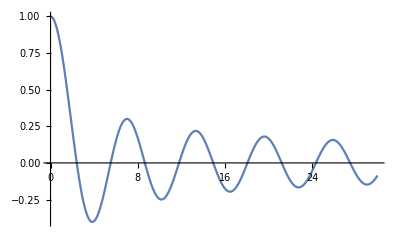

```mathematica
Plot[ Evaluate[gReplace[[2]][[1]] /. C[1]-> 1  /. k-> 1 ] , {t,0,30}]
```

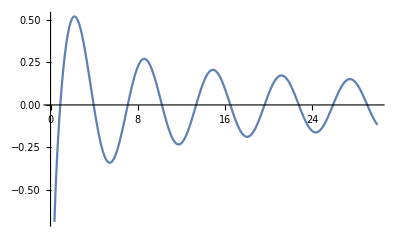

```mathematica
(*  Shows problelm at origin *) 
Plot[ Evaluate[gReplace[[2]][[2]] /. C[2]-> 1  /. k-> 1 ] , {t,0,30}]
```

```mathematica
(*  This gives some of the terms.... *) 
Clear[eq3pt26a]
eq3pt26a = 
 Asymptotic[( gReplace[[2]][[2]] /. C[2]-> 1  /. k-> 1 ) , {t,0,2}]
```

(2 EulerGamma)/π+t^2/(2 π)-(EulerGamma t^2)/(2 π)+(2 Log[t/2])/π-(t^2 Log[t/2])/(2 π)

## Derivation of Metric 3.70

```mathematica
Clear[eq3pt69]
eq3pt69 = 
- dτ^2+ τ^2 dl^2
```

-dτ^2+dl^2 τ^2

```mathematica
Clear[eq3pt69a]
eq3pt69a = 
dl^2-> dχ^2+ Sinh[χ]^2 ( Sin[θ]^2 dϕ^2+ dθ^2)
```

dl^2→dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2

```mathematica
lineToMetric[ eq3pt69a[[2]]  , {dχ,dθ,dϕ}] // MatrixForm
```

(1 | 0 | 0
0 | Sinh[χ]^2 | 0
0 | 0 | Sin[θ]^2 Sinh[χ]^2)

```mathematica
eq3pt69 /. eq3pt69a
```

-dτ^2+τ^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2)

```mathematica
Clear[metric3pt69]
metric3pt69 = 
lineToMetric[ eq3pt69 /. eq3pt69a  , {dτ,dχ,dθ,dϕ}]  ; 
metric3pt69// MatrixForm
```

(-1 | 0 | 0 | 0
0 | τ^2 | 0 | 0
0 | 0 | τ^2 Sinh[χ]^2 | 0
0 | 0 | 0 | τ^2 Sin[θ]^2 Sinh[χ]^2)

```mathematica
Clear[eq3pt70]
eq3pt70 = {
Sinh[ρ] == Sinh[χ] Sin[θ] , 
Cosh[ρ] Sinh[z] == Sinh[χ] Cos[θ]
} ;
eq3pt70 // TableForm
```

Sinh[ρ]==Sin[θ] Sinh[χ]
Cosh[ρ] Sinh[z]==Cos[θ] Sinh[χ]

```mathematica
Flatten[Solve[ eq3pt70 , {χ,θ}][[3]]] /. C[1]-> 0  /. C[2]-> 0  // Expand // Simplify // PowerExpand
```

{χ→ArcSinh[√(Cosh[ρ]^2 Sinh[z]^2+Sinh[ρ]^2)],θ→ArcTan[(Cosh[ρ] Sinh[z])/(√(Cosh[ρ]^2 Sinh[z]^2+Sinh[ρ]^2)),Sinh[ρ]/(√(Cosh[ρ]^2 Sinh[z]^2+Sinh[ρ]^2))]}

```mathematica
Dt[ eq3pt70  ] /. dtReplace // TableForm
```

dρ Cosh[ρ]==dχ Cosh[χ] Sin[θ]+dθ Cos[θ] Sinh[χ]
dz Cosh[z] Cosh[ρ]+dρ Sinh[z] Sinh[ρ]==dχ Cos[θ] Cosh[χ]-dθ Sin[θ] Sinh[χ]

```mathematica
Flatten[Solve[ ( Dt[ eq3pt70  ] /. dtReplace  ) , {dχ,dθ}]] // Expand // Simplify
```

{dχ→Sech[χ] (dz Cos[θ] Cosh[z] Cosh[ρ]+dρ Cosh[ρ] Sin[θ]+dρ Cos[θ] Sinh[z] Sinh[ρ]),dθ→Cos[θ] Csch[χ] (-dρ Sinh[z] Sinh[ρ] Tan[θ]+Cosh[ρ] (dρ-dz Cosh[z] Tan[θ]))}

```mathematica
Flatten[Solve[ ( Dt[ eq3pt70  ] /. dtReplace  ) , {dχ,dθ}]]  /. ( Flatten[Solve[ eq3pt70 , {χ,θ}][[3]]] /. C[1]-> 0  /. C[2]-> 0  // Expand // Simplify  ) // Expand // Simplify // TableForm
```

dχ→(√(Cosh[z]^2 Cosh[ρ]^2) Sech[z] Sech[ρ] (dz Cosh[ρ] Sinh[z]+dρ Cosh[z] Sinh[ρ]))/(√(Cosh[ρ]^2 Sinh[z]^2+Sinh[ρ]^2))
dθ→(Csch[z] (dρ Sech[ρ]^2-dz Coth[z] Tanh[ρ]))/(1+Csch[z]^2 Tanh[ρ]^2)

```mathematica
eq3pt69a
```

dl^2→dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2

```mathematica
Clear[eq3pt71a]
eq3pt71a = 
 eq3pt69a /. ( Flatten[Solve[ eq3pt70 , {χ,θ}][[3]]] /. C[1]-> 0  /. C[2]-> 0  // Expand // Simplify  ) /. (Flatten[Solve[ ( Dt[ eq3pt70  ] /. dtReplace  ) , {dχ,dθ}]]  /. ( Flatten[Solve[ eq3pt70 , {χ,θ}][[3]]] /. C[1]-> 0  /. C[2]-> 0  // Expand // Simplify  ) // Expand // Simplify) // Expand   ;
```

```mathematica
Clear[metric3pt71]
metric3pt71 = 
lineToMetric[ Collect[ eq3pt71a[[2]]  ,{ dρ^2, dϕ^2, dz^2}] , {dρ,dϕ,dz}] // Simplify   ;
metric3pt71 // MatrixForm
```

(1 | 0 | 0
0 | Sinh[ρ]^2 | 0
0 | 0 | Cosh[ρ]^2)

```mathematica
Clear[eq3pt71]
eq3pt71 = 
dl^2-> metricToLine[ metric3pt71 , {dρ,dϕ,dz}]
```

dl^2→dρ^2+dz^2 Cosh[ρ]^2+dϕ^2 Sinh[ρ]^2

```mathematica
Clear[eq3pt71b]
eq3pt71b = 
τ == Exp[t]
```

τ==ⅇ^t

```mathematica
eq3pt71b  /. Equal-> Rule
```

τ→ⅇ^t

```mathematica
Dt[ eq3pt71b ] /. dtReplace
```

dτ==dt ⅇ^t

```mathematica
Flatten[Solve[ ( Dt[ eq3pt71b ] /. dtReplace  ) , dτ ] ] /. ( eq3pt71b  /. Equal-> Rule  )
```

{dτ→dt ⅇ^t}

```mathematica
( eq3pt69 /. eq3pt69a ) /. ( eq3pt71b  /. Equal-> Rule  ) /. (Flatten[Solve[ ( Dt[ eq3pt71b ] /. dtReplace  ) , dτ ] ] /. ( eq3pt71b  /. Equal-> Rule  ) )
```

-dt^2 ⅇ^(2 t)+ⅇ^(2 t) (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[χ]^2)

## Line Element and Metric 4.3

```mathematica
Clear[eq4pt3]
eq4pt3 = 
Exp[2(γ-ψ)](dρ^2-dt^2) + ρ^2 Exp[-2ψ] dϕ^2+ Exp[2ψ](dz + ω dϕ)^2
```

(-dt^2+dρ^2) ⅇ^(2 (γ-ψ))+dϕ^2 ⅇ^(-2 ψ) ρ^2+ⅇ^(2 ψ) (dz+dϕ ω)^2

```mathematica
lineToMetric[ eq4pt3 , {dt,dρ,dϕ,dz}] // MatrixForm // pdConv
```

(-ⅇ^(2 γ-2 ψ) | 0 | 0 | 0
0 | ⅇ^(2 γ-2 ψ) | 0 | 0
0 | 0 | ρ^2 ⅇ^(-2 ψ)+ⅇ^(2 ψ) ω^2 | ⅇ^(2 ψ) ω
0 | 0 | ⅇ^(2 ψ) ω | ⅇ^(2 ψ))

```mathematica
Clear[eq4pt3a]
eq4pt3a = {
γ-> γ[t,ρ] , 
ψ-> ψ[t,ρ] , 
ω-> ω[t,ρ]
} ;
eq4pt3a // TableForm
```

γ→γ[t,ρ]
ψ→ψ[t,ρ]
ω→ω[t,ρ]

```mathematica
Clear[metric4pt3]
metric4pt3 = 
lineToMetric[ eq4pt3 , {dt,dρ,dϕ,dz}]  /. eq4pt3a  ;
metric4pt3 // MatrixForm // pdConv
```

(-ⅇ^(2 γ(t,ρ)-2 ψ(t,ρ)) | 0 | 0 | 0
0 | ⅇ^(2 γ(t,ρ)-2 ψ(t,ρ)) | 0 | 0
0 | 0 | ρ^2 ⅇ^(-2 ψ(t,ρ))+ⅇ^(2 ψ(t,ρ)) (ω(t,ρ))^2 | ⅇ^(2 ψ(t,ρ)) ω(t,ρ)
0 | 0 | ⅇ^(2 ψ(t,ρ)) ω(t,ρ) | ⅇ^(2 ψ(t,ρ)))

## Line Element and Metric 4.9

```mathematica
Clear[eq4pt9]
eq4pt9 = 
f[t,ρ](dρ^2-dt^2) + ρ( Exp[Φ[t,ρ]] dϕ^2+Exp[-Φ[t,ρ]] dz^2 )
```

(dz^2 ⅇ^(-Φ[t,ρ])+dϕ^2 ⅇ^Φ[t,ρ]) ρ+(-dt^2+dρ^2) f[t,ρ]

```mathematica
Clear[metric4pt9]
metric4pt9 = 
lineToMetric[ eq4pt9 , {dt,dρ,dϕ,dz} ]  ;
metric4pt9 // MatrixForm // pdConv
```

(-f(t,ρ) | 0 | 0 | 0
0 | f(t,ρ) | 0 | 0
0 | 0 | ρ ⅇ^(Φ(t,ρ)) | 0
0 | 0 | 0 | ρ ⅇ^(-Φ(t,ρ)))

```mathematica
(*
Section 4.3 Saifer and Piran
*)
```